Read me

This notebook can be used to reproduce the figures of “Deep hybrid classical-quantum reservoir computing for temporal quantum data processing” (https://arxiv.org/abs/2401.16961). It requires a working installation of a recent version of Wolfram Mathematica. It has been tested in Wolfram Mathematica 11.2 for Microsoft Windows (64-bit). 

To use it, evaluate Section 1 first. The global parameter “reps” inside subsection 1.2 controls how many samples are used to generate the ensemble averages and is by default set to 8. In “Deep hybrid classical-quantum reservoir computing for temporal quantum data processing” a value of 100 has been used, which of course takes much longer.

Then you can reproduce the figures in their own Sections in any order. Inside each Section cells should in general be evaluated in order, i.e. plots can be made only after data has been generated and so on.

The author of this notebook is Johannes Nokkala. Any inquiries about its contents can be sent to jsinok@utu.fi

Summary of the license
This work is licensed under CC BY 4.0. You are free to share and adapt the material as long as it remains under the same license  and you give appropriate credit. For the full legal text see LICENSE in the main repository: https://github.com/jsinok/DeephybridQRC

1 Preliminaries

We will clear all values, definitions, attributes, messages, and defaults associated with symbols in the global context. This is to prevent problems with pre-existing symbol definitions.

```mathematica
ClearAll["Global`*"];
```

We will set the history length to 0 to keep memory consumption in check. That is to say none of the previous input and output lines are saved by default for later use, only the ones we explicitly keep.

```mathematica
$HistoryLength=0;
```

Parallelization is used to speed up certain parts of the computations. We launch the maximum number of them now.

```mathematica
If[$ProcessorCount-$KernelCount>0,Quiet@LaunchKernels[$ProcessorCount-$KernelCount]];
```

## 1.1 User defined functions

### Auxiliary

#### Permutation

```mathematica
Clear[getmatP];
getmatP=Function[n,IdentityMatrix[2n][[Riffle[Range[n],Range[n]+n]]]];
```

#### Symplectic form

```mathematica
Clear[getmatΩ];
getmatΩ=Function[n,
KroneckerProduct[IdentityMatrix[n,WorkingPrecision->MachinePrecision],({{0, 1}, {-1, 0}})]
];
```

#### blockArray

```mathematica
(*can be used to create a block diagonal matrix as sparse array*)
Clear[blockArray];
blockArray[mat_]:=SparseArray[Tuples[Range@#-{1,0,0}].{Rest@#,{1,0},{0,1}}&@Dimensions@mat->Flatten@mat];
```

```mathematica
(*can be used to create a block diagonal matrix as packed array*)
Clear[blockArray];
blockArray[mat_]:=Developer`ToPackedArray[Normal@SparseArray[Tuples[Range@#-{1,0,0}].{Rest@#,{1,0},{0,1}}&@Dimensions@mat->Flatten@mat],Real];
```

### State related

```mathematica
Clear[getσQuadratures];
getσQuadratures=Function[{nth,r,ϕ},ConstantArray[1.+2. nth,{2,2}]×({{Cosh[2r]+Cos[ϕ]Sinh[2r], Sin[ϕ]Sinh[2r]}, {Sin[ϕ]Sinh[2r], Cosh[2r]-Cos[ϕ]Sinh[2r]}})];
```

```mathematica
Clear[getσSTSQuadratures];
getσSTSQuadratures=Function[{nth,r},ConstantArray[1+2 nth,{4,4}]×({{Cosh[2 r], 0., Sinh[2 r], 0.}, {0., Cosh[2 r], 0., -Sinh[2 r]}, {Sinh[2 r], 0., Cosh[2 r], 0.}, {0., -Sinh[2 r], 0., Cosh[2 r]}})];
```

```mathematica
Clear[loganegaQuadratures];
loganegaQuadratures=Compile[{{σAB,_Real,2}},
With[
{σA=σAB[[1;;2,1;;2]],
σB=σAB[[3;;4,3;;4]],
σC=σAB[[1;;2,3;;4]]},
With[{
detσA=-σA⟦1,2⟧ σA⟦2,1⟧+σA⟦1,1⟧ σA⟦2,2⟧,
detσB=-σB⟦1,2⟧ σB⟦2,1⟧+σB⟦1,1⟧ σB⟦2,2⟧,
detσC=-σC⟦1,2⟧ σC⟦2,1⟧+σC⟦1,1⟧ σC⟦2,2⟧,
detσAB=σAB⟦1,4⟧ σAB⟦2,3⟧ σAB⟦3,2⟧ σAB⟦4,1⟧-σAB⟦1,3⟧ σAB⟦2,4⟧ σAB⟦3,2⟧ σAB⟦4,1⟧-σAB⟦1,4⟧ σAB⟦2,2⟧ σAB⟦3,3⟧ σAB⟦4,1⟧+σAB⟦1,2⟧ σAB⟦2,4⟧ σAB⟦3,3⟧ σAB⟦4,1⟧+σAB⟦1,3⟧ σAB⟦2,2⟧ σAB⟦3,4⟧ σAB⟦4,1⟧-σAB⟦1,2⟧ σAB⟦2,3⟧ σAB⟦3,4⟧ σAB⟦4,1⟧-σAB⟦1,4⟧ σAB⟦2,3⟧ σAB⟦3,1⟧ σAB⟦4,2⟧+σAB⟦1,3⟧ σAB⟦2,4⟧ σAB⟦3,1⟧ σAB⟦4,2⟧+σAB⟦1,4⟧ σAB⟦2,1⟧ σAB⟦3,3⟧ σAB⟦4,2⟧-σAB⟦1,1⟧ σAB⟦2,4⟧ σAB⟦3,3⟧ σAB⟦4,2⟧-σAB⟦1,3⟧ σAB⟦2,1⟧ σAB⟦3,4⟧ σAB⟦4,2⟧+σAB⟦1,1⟧ σAB⟦2,3⟧ σAB⟦3,4⟧ σAB⟦4,2⟧+σAB⟦1,4⟧ σAB⟦2,2⟧ σAB⟦3,1⟧ σAB⟦4,3⟧-σAB⟦1,2⟧ σAB⟦2,4⟧ σAB⟦3,1⟧ σAB⟦4,3⟧-σAB⟦1,4⟧ σAB⟦2,1⟧ σAB⟦3,2⟧ σAB⟦4,3⟧+σAB⟦1,1⟧ σAB⟦2,4⟧ σAB⟦3,2⟧ σAB⟦4,3⟧+σAB⟦1,2⟧ σAB⟦2,1⟧ σAB⟦3,4⟧ σAB⟦4,3⟧-σAB⟦1,1⟧ σAB⟦2,2⟧ σAB⟦3,4⟧ σAB⟦4,3⟧-σAB⟦1,3⟧ σAB⟦2,2⟧ σAB⟦3,1⟧ σAB⟦4,4⟧+σAB⟦1,2⟧ σAB⟦2,3⟧ σAB⟦3,1⟧ σAB⟦4,4⟧+σAB⟦1,3⟧ σAB⟦2,1⟧ σAB⟦3,2⟧ σAB⟦4,4⟧-σAB⟦1,1⟧ σAB⟦2,3⟧ σAB⟦3,2⟧ σAB⟦4,4⟧-σAB⟦1,2⟧ σAB⟦2,1⟧ σAB⟦3,3⟧ σAB⟦4,4⟧+σAB⟦1,1⟧ σAB⟦2,2⟧ σAB⟦3,3⟧ σAB⟦4,4⟧
},
Ramp[Re[-Log[2,Sqrt[(1/2(detσA+detσB-2detσC-√((detσA+detσB-2detσC)^2-4detσAB)))]]]]
]
],RuntimeAttributes->{Listable},Parallelization->True
];
```

### Real-time QRC generator

#### Coupling matrices g & h, featuring the sparsity parameter p

```mathematica
gmin=0.1;
gmax=0.3;
```

```mathematica
Clear[getmatg];
getmatg=Function[{n,p},
With[
{
matran=RandomChoice[{1-p,p}->{0,1},{n,n}]RandomReal[{gmin,gmax},{n,n}]
},
matran//UpperTriangularize[#,1]&//#+#ᵀ&
]
];
```

```mathematica
hmin=0.2;
hmax=0.4;
```

```mathematica
Clear[getmath];
getmath=Function[{n,p},
With[
{
matran=RandomChoice[{1-p,p}->{0,1},{n,n}]RandomReal[{hmin,hmax},{n,n}]
},
matran//UpperTriangularize[#,1]&//#+#ᵀ&
]
];
```

#### Matrix M in the basis of creation and annihilation operators

```mathematica
Clear[getmatMcrean];
getmatMcrean=Function[{n,ω,p},
With[
{
math=getmath[n,p],
matg=getmatg[n,p]
},ArrayFlatten[({{matg, I math}, {-I math, matg}})]+ω IdentityMatrix[2n]
]
];
```

#### Basis change matrix from creation and annihilation operators to quadrature operators

```mathematica
Clear[getmatG];
getmatG=Function[n,({{IdentityMatrix[n], IdentityMatrix[n]}, {-I IdentityMatrix[n], I IdentityMatrix[n]}})//ArrayFlatten];
```

#### Matrix M in the basis of quadrature operators, re-generated until stable

```mathematica
Clear[getmatMmaybestable];
getmatMmaybestable=Function[{n,ω,p},
With[
{
matG=getmatG[n],
matP=getmatP[n]
},
matP.matG.getmatMcrean[n,ω,p].matG†.matPᵀ//Re(*real by construction but Re gets rid of terms like 0.I*)
]
];
```

```mathematica
Clear[getmatM];
getmatM=Function[{n,ω,p},
Block[{result},
While[Min[Eigenvalues[result=getmatMmaybestable[n,ω,p]]]<0];
result]
];
```

#### The symplectic matrix

```mathematica
Clear[getmatrixSΔtJorgeScheme];
getmatrixSΔtJorgeScheme=Function[{n,bigR,p},
With[
{
ω=1.(*always unit frequency*)
},
With[
{
Δt=1./ω,(*always unit time spent inside both χ^(2)crystals*)
matM1=getmatM[n,ω,p],
matM2=getmatM[n,ω,p],
matΩ=getmatΩ[n]
},
With[
{
matS1Δt=MatrixExp[matΩ.matM1 Δt],
matS2Δt=MatrixExp[matΩ.matM2 Δt]
},
With[
{
matSΔt=({{√bigR matS1Δt, -√(1.-bigR)matS1Δt}, {√(1.-bigR)matS2Δt, √bigR matS2Δt}})//ArrayFlatten
},
matSΔt
]
]
]
]
];
```

#### Initial state generator

```mathematica
Clear[makegetinitstateQuadratures];
makegetinitstateQuadratures=Function[n,
Module[
{
getinit
},
getinit[]:=IdentityMatrix[4n,WorkingPrecision->MachinePrecision];
getinit
]
];
```

#### Preprocess

The input is assumed to be a list of covariance matrices of single mode Gaussian states. The preprocess duplicates each to make a product state with N modes.

```mathematica
Clear[getpreprocessQuadraturesQ];
getpreprocessQuadraturesQ=Function[{n},
Function[listinput,Transpose[KroneckerProduct[IdentityMatrix[n],Transpose[listinput,{3,1,2}]],{2,3,1}]]
];
```

In, e.g., the entanglement detection task the inputs are bipartite states. Then we need to use less duplicates to get N modes.

```mathematica
Clear[gettwomodepreprocess];
gettwomodepreprocess[n_?EvenQ]:=With[
{
nhalf=n/2
},
Function[listinput,Transpose[KroneckerProduct[IdentityMatrix[nhalf],Transpose[listinput,{3,1,2}]],{2,3,1}]]
];
gettwomodepreprocess[n_?OddQ]:=With[
{
nhalf=(n-1)/2
},Function[listinput,ArrayFlatten[({{#, 0.}, {0., getσQuadratures[0,0,0]}})]&/@Transpose[KroneckerProduct[IdentityMatrix[nhalf],Transpose[listinput,{3,1,2}]],{2,3,1}]]
];
gettwomodepreprocess[1]:=Function[listinput,ConstantArray[getσQuadratures[0,0,0],Length[listinput]]];
```

#### Update rule

```mathematica
Clear[getupdateQuadratures];
getupdateQuadratures=Function[matSΔt,
With[
{
n=Length[matSΔt]/4
},
Function[{σprev,σAnew},matSΔt.ArrayFlatten[({{σprev[[;;2n,;;2n]], 0.}, {0., σAnew}})].matSΔtᵀ]
]
];
```

#### Readout

Pick the distinct terms featuring only output position operators from the full covariance matrix.

```mathematica
Clear[getreadoutQuadratures];
getreadoutQuadratures=Function[n,
With[
{
selector=ConstantArray[1,{n,n}]//UpperTriangularize//Flatten
},
Function[covariances,
(covariances[[All,Range[1,2n,2]+2n,Range[1,2n,2]+2n]])//Map[Pick[Flatten[#],selector,1]&]//Developer`ToPackedArray
]
]
];
```

This readout is used in the finite samples case and features the Wishart random matrix distribution. Symmetricity is enforced for technical reasons (σx is supposed to be symmetric by construction).

```mathematica
Clear[getreadoutQuadraturesM];
getreadoutQuadraturesM=Function[{n,bigM},
With[
{
selector=ConstantArray[1,{n,n}]//UpperTriangularize//Flatten,
bigMinverse=1./bigM
},
Function[covariances,
With[
{
listσx=covariances[[All,Range[1,2n,2]+2n,Range[1,2n,2]+2n]]
},
(bigMinverse Table[RandomVariate[WishartMatrixDistribution[bigM,σx]],{σx,0.5(Transpose[listσx,{1,3,2}]+listσx)}])//Map[Pick[Flatten[#],selector,1]&]//Developer`ToPackedArray
]
]
]
];
```

#### Generator proper, Q input

```mathematica
Clear[makerandomJorgeQRCforQinput];
makerandomJorgeQRCforQinput[n_,bigR_,p_]:=
With[
{
matSΔt=getmatrixSΔtJorgeScheme[n,bigR,p]
},
{
getupdateQuadratures[matSΔt],
makegetinitstateQuadratures[n],
getpreprocessQuadraturesQ[n],
getreadoutQuadratures[n]
}
];

makerandomJorgeQRCforQinput[n_,bigR_,p_,bigM_]:=
With[
{
matSΔt=getmatrixSΔtJorgeScheme[n,bigR,p]
},
{
getupdateQuadratures[matSΔt],
makegetinitstateQuadratures[n],
getpreprocessQuadraturesQ[n],
getreadoutQuadraturesM[n,bigM]
}
];

makerandomJorgeQRCforQinput[n_,bigR_,p_,∞]:=
makerandomJorgeQRCforQinput[n,bigR,p];
```

### ESN generator

#### Random weights matrix and random weights vector generators

```mathematica
(*can control sparsity with p; the matrix is scaled by its largest singular value*)
Clear[getrandomweigthsmatrix];
getrandomweigthsmatrix[nESN_,p_]:=With[{matrixWunscaled=RandomChoice[{1.-p,p}->{0.,1.},{nESN,nESN}]RandomReal[{-1.,1.},{nESN,nESN}]},
matrixWunscaled/First[SingularValueList[matrixWunscaled,1]]
];

(*spatial multiplexing with single component is trivial*)
getrandomweigthsmatrix[nESN_,p_,1]:=getrandomweigthsmatrix[nESN,p];

(*spatial multiplexing with spat>1 components creates a block diagonal weights matrix as sparse array*)
getrandomweigthsmatrix[nESN_,p_,spat_]:=blockArray[Table[getrandomweigthsmatrix[nESN,p],{spat}]];

(*memoization when called with seed*)
getrandomweigthsmatrix[nESN_,p_,spat_,seed_]:=getrandomweigthsmatrix[nESN,p,spat,seed]=(SeedRandom[seed];getrandomweigthsmatrix[nESN,p,spat]);
```

```mathematica
(*similar to above*)
Clear[getrandomweightsvector];
getrandomweightsvector[nESN_]:=RandomReal[{-1.,1.},nESN];

getrandomweightsvector[nESN_,seed_]:=getrandomweightsvector[nESN,seed]=(SeedRandom[seed];getrandomweightsvector[nESN]);
```

#### Initial state generator

```mathematica
Clear[makegetinit];
makegetinit[nESN_]:=Module[{getinit},getinit[]:=RandomReal[{-1.,1.},nESN];getinit[seed_]:=BlockRandom[SeedRandom[seed];RandomReal[{-1.,1.},nESN]];getinit];
```

#### HD readout straight to ESN

```mathematica
Clear[getESNonlyreadoutQuadraturesM];
getESNonlyreadoutQuadraturesM=Function[{n,bigM},
With[
{
selector=ConstantArray[1,{n,n}]//UpperTriangularize//Flatten,
bigMinverse=1./bigM
},
Function[covariances,
With[
{
listσx=covariances[[All,Range[1,2n,2],Range[1,2n,2]]]
},
(bigMinverse Table[RandomVariate[WishartMatrixDistribution[bigM,σx]],{σx,0.5(Transpose[listσx,{1,3,2}]+listσx)}])//Map[Pick[Flatten[#],selector,1]&]//Developer`ToPackedArray
]
]
]
];
```

#### Coercion matrix

```mathematica
Clear[getcoercionmatrix];
getcoercionmatrix=Function[{nESN,nObs},With[{matrixWunscaled=RandomReal[{-1.,1.},{nESN,nObs}]},
matrixWunscaled/First[SingularValueList[matrixWunscaled,1]]
]
];
```

#### Random ESN with the coercion matrix generator proper

```mathematica
makerandomESNcoerced[nESN_,ρ_,ι_,afun_,p_,spat_,inputdimension_]:=
With[
{matrixW=getrandomweigthsmatrix[nESN,p,spat],coerciomatrix=getcoercionmatrix[nESN spat,inputdimension]},
{
afun[ρ matrixW.#1+ι coerciomatrix.#2]&(*update*),
makegetinit[spat nESN](*initial state generator*),
Identity(*preprocess*),
Identity(*readout*)
}
];
```

### Q-to-C tasks

#### Input generators

```mathematica
(*covariance matrices of random singe mode input states*)
With[
{
nthmin=0.,
nthmax=5.,
rmin=0.,
rmax=0.75,
ϕmin=0.,
ϕmax=2.Pi
},
Clear[generateInputState];
generateInputState=Function[{length},Transpose[getσQuadratures[RandomReal[{nthmin,nthmax},length],RandomReal[{rmin,rmax},length],RandomReal[{ϕmin,ϕmax},length]],{2,3,1}]]
];
```

#### Target generators

```mathematica
(*assumes single mode cov mat!*)
(*get the trace of a matrix*)
(*listable: list of matrices gives a list of traces*)
Clear[getTargetTrace];
getTargetTrace=Compile[{{matrix,_Real,2}},Total@Table[matrix[[i,i]],{i,1,Length[matrix]}],RuntimeAttributes->{Listable}];
```

```mathematica
(*add a delay*)
(*delay accomplished with cyclical permutation*)
Clear[getTargetTracedelay];
getTargetTracedelay=Function[{listinput,delay},
RotateRight[getTargetTrace[listinput],delay]];
```

```mathematica
(*an element of the cov mat, with indices as parameter*)
Clear[getTargetElement];
getTargetElement=Function[{listinput,i,j},listinput[[All,i,j]]];
```

```mathematica
(*add a delay*)
(*delay accomplished with cyclical permutation*)
Clear[getTargetElementDelay];
getTargetElementDelay=Function[{listinput,i,j,delay},RotateRight[getTargetElement[listinput,i,j],delay]];
```

```mathematica
Clear[gettargetDet];
gettargetDet=Function[{listinput},Det/@listinput];
```

```mathematica
(*add a delay*)
(*delay accomplished with cyclical permutation*)
Clear[gettargetDetDelay];
gettargetDetDelay=Function[{listinput,delay},
RotateRight[gettargetDet[listinput],delay]];
```

#### Trace task

```mathematica
Clear[makeTraceTask];
makeTraceTask[]:={generateInputState,getTargetTracedelay,getNMSE};
```

#### Element task

```mathematica
Clear[makeElementTask];
makeElementTask[]:={generateInputState,getTargetElementDelay,getNMSE};
```

#### Determinant task

```mathematica
Clear[makeDetTask];
makeDetTask[]:={generateInputState,gettargetDetDelay,getNMSE};
```

### Get observables

```mathematica
getobservables=Function[{update,init,preprocess,listinput,readout},readout[Rest[FoldList[update,init,preprocess[listinput]]]]];
```

### Trainer tester

```mathematica
Clear[trainertester];
trainertester[listobservables_,listtarget_,prep_,train_,test_,figureofmerit_:getNMSE]:=Module[{listtargettrain,listtargettest,listX,listXtrain,listXtest,listW,listO},
(*extract the training and test phases of the target*)
{listtargettrain,listtargettest}={listtarget[[prep+1;;prep+train]],listtarget[[prep+train+1;;prep+train+test]]};
(*add the bias term to training and test phases of the observables*)
listX=ArrayFlatten[{{listobservables[[prep+1;;]],1.}}];
(*extract the training and test phases of the observables feat bias term*)
{listXtrain,listXtest}={listX[[1;;train]],listX[[train+1;;train+test]]};
(******************)
(*training and FOM*)
(******************)
listW=PseudoInverse[listXtrain].listtargettrain;
listO=listXtest.listW;
With[{weights=Most[listW],bias=Last[listW]},
{figureofmerit[listO,listtargettest](*figure of merit*),Function[listin,listin.weights+bias](*getoutput*)}]
];
```

### Hybrid trainer tester

More involved because the input to layer 2 depends on layer 1 etc.. Hence why there is no apparent way to decouple the trainer tester from the layers.

Also outputs the sandwich observables, unlike the single layer trainer tester!

```mathematica
Clear[hybridtrainertester];
hybridtrainertester=Function[{listinput,layer1,layer2,targets1,targets2,prep,train,test},
With[
{
listobservables1=getobservables[layer1[[1]],layer1[[2]][],layer1[[3]],listinput,layer1[[4]]]
},
With[
{
listinput2=Table[
trainertester[listobservables1,listtarget,prep,train,test][[2]][listobservables1],{listtarget,targets1}
]ᵀ(*trainertester[...][[2]] is the function that gives the output of the trained layer*)
},
With[
{
listobservables2=getobservables[layer2[[1]],layer2[[2]][],layer2[[3]],listinput2,layer2[[4]]]
},
With[
{
listsandwichobservables=Join[listobservables2,listobservables1,2]
},
{
Table[trainertester[listsandwichobservables,listtarget,prep,train,test],{listtarget,targets2}],listsandwichobservables
}
]
]
]
]
];
```

### Figures of merit

#### NMSE

```mathematica
getNMSE=Function[{listoutput,listtarget},Total[(listtarget-listoutput)^2]/Total[listtarget^2]];
```

#### Fidelity

(Uhlmann) fidelity between two single mode pure Gaussian states.

```mathematica
Clear[fidelitypurestatesQuadratures];
fidelitypurestatesQuadratures=Function[{σA,σB},
With[
{
fdetσ=Ramp[Chop[(Det[σA]-1)(Det[σB]-1)]](*by construction real and positive, here we enforce this*)(*if im part too large to be Chopped to 0, Ramp returns unevaluated to signal that something is wrong*)
},
Divide[2.,√(Det[σA+σB]+fdetσ)-√fdetσ]
]
];
```

## 1.2 Global parameter: number of random realizations

```mathematica
reps=8;
```

Fig. 2, longer short-term memory

## State probing task, random ensemble, multiple delays divided ceiling and floor half

```mathematica
seed=258;
```

### Generate the task

#### Parameters for the task

```mathematica
{prep,train,test}={500,3000,1000};
listτ=Range[0,20];
```

#### The task proper

```mathematica
{getrandominput,gettarget,figureofmerit}=makeElementTask[];
```

### Parameters for the RC

#### Parameters for the Q reservoir

```mathematica
n=9;
bigR=0.4;
p=7./9;
```

```mathematica
listbigM={100,1000,10000,100000,1000000,∞};
```

#### Parameters for the ESN RC

```mathematica
nESN=(n^2-n)/2+n;
ρ0=0.7;
ι0=Power[10.,-4/3];
pESN=1.;(*sparsity parameter for the ESN*)
spatESN=1;(*order of spatial multiplexing*)
myafun={Tanh(*Tanh*),Ramp(*ReLu*),Function[x,Ramp[x]-0.01Ramp[-x]](*leaky ReLu*),Function[x,x](*identity (linear ESN)*),Function[x,Log[1.+Exp[x]]](*softmax*)}[[-1]];
```

### Computations

```mathematica
SeedRandom[seed];
listparallelseeds=RandomInteger[1*^6{-1,1},$KernelCount];
ParallelEvaluate[SeedRandom[listparallelseeds[[$KernelID]]]];
```

#### For the hybrid system

```mathematica
done=0;SetSharedVariable[done]
```

```mathematica
Monitor[listresultsbigM=ParallelTable[
(*random input*)
listinput=getrandominput[prep+train+test];
(*all targets for this delay*)
listtargetQ={
gettarget[listinput,1,1,Ceiling[delay/2]],
gettarget[listinput,1,2,Ceiling[delay/2]],
gettarget[listinput,2,2,Ceiling[delay/2]]
};
listtargetC={
gettarget[listinput,1,1,delay],
gettarget[listinput,1,2,delay],
gettarget[listinput,2,2,delay]
};
(*call hybridtrainertester*)
{listNMSEsAndgetoutputs,listobservablesSandwich}=hybridtrainertester[listinput,
makerandomJorgeQRCforQinput[n,bigR,p,bigM],
makerandomESNcoerced[nESN,ρ0,ι0,myafun,pESN,spatESN,Length[listtargetQ]],
listtargetQ,listtargetC,prep,train,test];
listgetoutputs=listNMSEsAndgetoutputs[[All,2]];
(*put the states together to compute the final figure of merit, the mean fidelity*)
listoutputtest=Transpose[({{listgetoutputs[[1]][listobservablesSandwich[[prep+train+1;;]]], listgetoutputs[[2]][listobservablesSandwich[[prep+train+1;;]]]}, {listgetoutputs[[2]][listobservablesSandwich[[prep+train+1;;]]], listgetoutputs[[3]][listobservablesSandwich[[prep+train+1;;]]]}}),{2,3,1}];
listtargettest=Transpose[({{listtargetC[[1,prep+train+1;;]], listtargetC[[2,prep+train+1;;]]}, {listtargetC[[2,prep+train+1;;]], listtargetC[[3,prep+train+1;;]]}}),{2,3,1}];
listfidelity=MapThread[fidelitypurestatesQuadratures,{listoutputtest,listtargettest}];
listfidelitygoodcases=Select[listfidelity,(#∈Reals&&0≤#≤1)&];
(*increment done*)
done+=1;
(*finally!*)
Mean@listfidelitygoodcases,
{reps},{delay,listτ},{bigM,listbigM}],ProgressIndicator[done,{0,reps Length[listτ]Length[listbigM]}]];//AbsoluteTiming//First
```

155.544

### Make some plots

```mathematica
(listresultsbigMmean=Transpose[listresultsbigM,{3,2,1}]//Map[Mean,#,{2}]&)//Dimensions
```

{6,21}

```mathematica
listbigMlbls=Table[
With[
{
e=e
},
Style[ToString[HoldForm[10^e],TraditionalForm],12]],{e,Log[10,Most@listbigM]}
]~Join~{"∞"}
```

{10^2,10^3,10^4,10^5,10^6,∞}

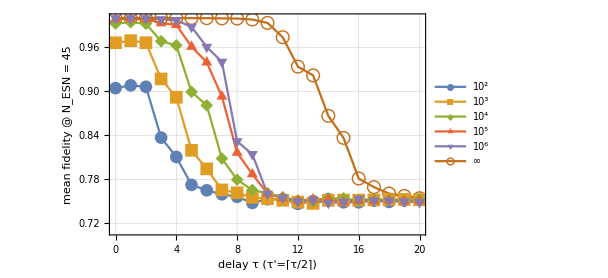

```mathematica
plotbigMresultsI=listresultsbigMmean//ListLinePlot[#,
ImageSize->450,
LabelStyle->15,
Frame->True,
GridLines->Automatic,
PlotRange->{All,{0.71,All}},
DataRange->MinMax[listτ],
PlotLegends->Placed[
LineLegend[listbigMlbls,LegendLabel->Placed[Rotate[Style["ensemble size M",10],Pi/2],Left],LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->Thin,Background->White,FrameMargins->0,ContentPadding->False]&)],
Scaled[{0.89,0.63}]],
PlotMarkers->{Automatic, 13},
FrameLabel->{"delay τ (τ'=⌈τ/2⌉)","mean fidelity @ N_ESN = 45"},
PlotRangePadding->{Scaled[.03],Automatic}
]&
```

### Show plots

```mathematica
plotbigMresultsI
```

-Graphics-

## State probing task, random ensemble, multiple delays but ESN handles all of it.. two values for both ρ and ESN size

```mathematica
seed=42;
```

### Generate the task

#### Parameters for the task

```mathematica
{prep,train,test}={500,3000,1000};
listτ=Range[0,20];
```

#### The task proper

```mathematica
{getrandominput,gettarget,figureofmerit}=makeElementTask[];
```

### Parameters for the RC

#### Parameters for the Q reservoir

```mathematica
n=9;
bigR=0.4;
p=7./9;
```

#### Parameters for the ESN RC

```mathematica
nESN=(n^2-n)/2+n;
ρ0=0.7; 
ι0=Power[10.,-4/3];
pESN=1.;
spatESN=1;(*order of spatial multiplexing*)
myafun={Tanh(*Tanh*),Ramp(*ReLu*),Function[x,Ramp[x]-0.01Ramp[-x]](*leaky ReLu*),Function[x,x](*identity (linear ESN)*),Function[x,Log[1.+Exp[x]]](*softmax*)}[[-1]];
```

```mathematica
listρ0={0.7,1.8}
```

{0.7,1.8}

```mathematica
listnESN={45,295}
```

{45,295}

```mathematica
listbigM={100,1000,10000,100000,1000000,∞};
```

### Computations

```mathematica
SeedRandom[seed];
listparallelseeds=RandomInteger[1*^6{-1,1},$KernelCount];
ParallelEvaluate[SeedRandom[listparallelseeds[[$KernelID]]]];
```

#### For the hybrid system

```mathematica
done=0;SetSharedVariable[done]
```

```mathematica
With[
{
delay=5,
nESN=First[listnESN],
ρ0=First[listρ0]
},
With[
{
delayQRC=Ceiling[delay/2]
},
Monitor[listresultsbigMIIsmallESN=ParallelTable[
(*random input*)
listinput=getrandominput[prep+train+test];
(*all targets for this delay*)
listtargetQ={
gettarget[listinput,1,1,delayQRC],
gettarget[listinput,1,2,delayQRC],
gettarget[listinput,2,2,delayQRC]
};
listtargetC={
gettarget[listinput,1,1,delay],
gettarget[listinput,1,2,delay],
gettarget[listinput,2,2,delay]
};
(*call hybridtrainertester*)
{listNMSEsAndgetoutputs,listobservablesSandwich}=hybridtrainertester[listinput,
makerandomJorgeQRCforQinput[n,bigR,p,bigM](*random Jorge QRC instance*),
makerandomESNcoerced[nESN,ρ0,ι0,myafun,pESN,spatESN,Length[listtargetQ]](*random Jorge QRC instance*),
listtargetQ,listtargetC,prep,train,test];
listgetoutputs=listNMSEsAndgetoutputs[[All,2]];
(*put the states together to compute the final figure of merit, the mean fidelity*)
listoutputtest=Transpose[({{listgetoutputs[[1]][listobservablesSandwich[[prep+train+1;;]]], listgetoutputs[[2]][listobservablesSandwich[[prep+train+1;;]]]}, {listgetoutputs[[2]][listobservablesSandwich[[prep+train+1;;]]], listgetoutputs[[3]][listobservablesSandwich[[prep+train+1;;]]]}}),{2,3,1}];
listtargettest=Transpose[({{listtargetC[[1,prep+train+1;;]], listtargetC[[2,prep+train+1;;]]}, {listtargetC[[2,prep+train+1;;]], listtargetC[[3,prep+train+1;;]]}}),{2,3,1}];
listfidelity=MapThread[fidelitypurestatesQuadratures,{listoutputtest,listtargettest}];
listfidelitygoodcases=Select[listfidelity,(#∈Reals&&0≤#≤1)&];
(*increment done*)
done+=1;
(*finally!*)
Mean@listfidelitygoodcases,
{reps},{bigM,listbigM}],ProgressIndicator[done,{0,reps Length[listbigM]}]]
]
];//AbsoluteTiming//First
```

8.22905

```mathematica
done=0;
```

```mathematica
With[
{
delay=5,
nESN=Last[listnESN],
ρ0=Last[listρ0]
},
With[
{
delayQRC=0
},
Monitor[listresultsbigMIIbigESN=ParallelTable[
(*random input*)
listinput=getrandominput[prep+train+test];
(*all targets for this delay*)
listtargetQ={
gettarget[listinput,1,1,delayQRC],
gettarget[listinput,1,2,delayQRC],
gettarget[listinput,2,2,delayQRC]
};
listtargetC={
gettarget[listinput,1,1,delay],
gettarget[listinput,1,2,delay],
gettarget[listinput,2,2,delay]
};
(*call hybridtrainertester*)
{listNMSEsAndgetoutputs,listobservablesSandwich}=hybridtrainertester[listinput,
makerandomJorgeQRCforQinput[n,bigR,p,bigM](*random Jorge QRC instance*),
makerandomESNcoerced[nESN,ρ0,ι0,myafun,pESN,spatESN,Length[listtargetQ]](*random Jorge QRC instance*),
listtargetQ,listtargetC,prep,train,test];
listgetoutputs=listNMSEsAndgetoutputs[[All,2]];
(*put the states together to compute the final figure of merit, the mean fidelity*)
listoutputtest=Transpose[({{listgetoutputs[[1]][listobservablesSandwich[[prep+train+1;;]]], listgetoutputs[[2]][listobservablesSandwich[[prep+train+1;;]]]}, {listgetoutputs[[2]][listobservablesSandwich[[prep+train+1;;]]], listgetoutputs[[3]][listobservablesSandwich[[prep+train+1;;]]]}}),{2,3,1}];
listtargettest=Transpose[({{listtargetC[[1,prep+train+1;;]], listtargetC[[2,prep+train+1;;]]}, {listtargetC[[2,prep+train+1;;]], listtargetC[[3,prep+train+1;;]]}}),{2,3,1}];
listfidelity=MapThread[fidelitypurestatesQuadratures,{listoutputtest,listtargettest}];
listfidelitygoodcases=Select[listfidelity,(#∈Reals&&0≤#≤1)&];
(*increment done*)
done+=1;
(*finally!*)
Mean@listfidelitygoodcases,
{reps},{bigM,listbigM}],ProgressIndicator[done,{0,reps Length[listbigM]}]]
]
];//AbsoluteTiming//First
```

15.1578

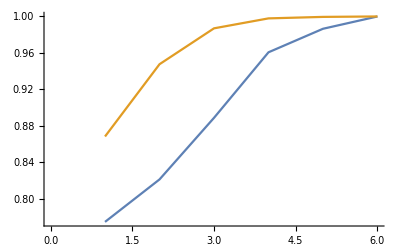

```mathematica
{Mean[listresultsbigMIIsmallESN],Mean[listresultsbigMIIbigESN]}//ListLinePlot
```

### Make some plots

```mathematica
listbigMlblsII=Table[
With[
{
e=e
},
Style[ToString[HoldForm[10^e],TraditionalForm],15]],{e,Log[10,Most@listbigM]}
]~Join~{Style["∞",15]}
```

{10^2,10^3,10^4,10^5,10^6,∞}

```mathematica
With[
{
legends={Column[{"N_ESN=45","ρ=0.7","τ'=⌈τ/2⌉"}],Column[{"N_ESN=295","ρ=1.8","τ'=0"}]}
},
plotbigMresultsII={MapAt[Callout[#,"τ'=⌈τ/2⌉"]&,Mean[listresultsbigMIIsmallESN],2],MapAt[Callout[#,"τ'=0"]&,Mean[listresultsbigMIIbigESN],2]}//ListLinePlot[#,
ImageSize->450,
LabelStyle->15,
Frame->True,
GridLines->Automatic,
PlotRange->{All,{0.74,All}},FrameTicks->{{Automatic,Automatic},{{Range[6],listbigMlblsII}ᵀ,Automatic}},
PlotMarkers->{Automatic, 13},
FrameLabel->{"ensemble size M","mean fidelity @ τ=5"},
PlotRangePadding->{Scaled[.03],Automatic},
PlotLegends->Placed[
LineLegend[listnESN,LegendLabel->Style[Column[{"ESN size","N_ESN"}],10],LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->Thin,Background->White,FrameMargins->0,ContentPadding->False]&)],
Scaled[{0.85,0.55}]]
]&
]
```

-Graphics-

### Show plots

```mathematica
plotbigMresultsII
```

-Graphics-

## Put them together

```mathematica
plotMcombo=Grid[{{plotbigMresultsI},{plotbigMresultsII}}]
```

-Graphics-

Fig. 3, nonlinear memory

## Trace task, random ensemble, fixed delay handled equally as the sizes are varied

```mathematica
time=AbsoluteTime[];
seed=1947;
```

### Generate the task

#### Parameters for the task

```mathematica
{prep,train,test}={500,3000,1000};
delay=2;
```

#### The task proper

```mathematica
{getrandominput,gettarget,figureofmerit}=makeTraceTask[];
```

### Parameters for the RC

#### Parameters for the QHON RC (bare frequency as in task)

```mathematica
listn=Range[1,9,2];
bigR=0.4;
p=7./9;
bigM=100000;
```

#### Parameters for the ESN RC

```mathematica
listnESN=(listn^2-listn)/2+listn;
ρ0=0.7; 
ι0=Power[10.,-4/3]; 
pESN=1.;
spatESN=1;
myafun={Tanh(*Tanh*),Ramp(*ReLu*),Function[x,Ramp[x]-0.01Ramp[-x]](*leaky ReLu*),Function[x,x](*identity (linear ESN)*),Function[x,Log[1.+Exp[x]]](*softmax*)}[[-1]];
```

### Computations

```mathematica
SeedRandom[seed];
listparallelseeds=RandomInteger[1*^6{-1,1},$KernelCount];
ParallelEvaluate[SeedRandom[listparallelseeds[[$KernelID]]]];
```

```mathematica
done=0;SetSharedVariable[done]
```

```mathematica
Monitor[listresults=ParallelTable[
(*random input*)
listinput=getrandominput[prep+train+test];
(*all targets for this delay*)
listtargetQ={gettarget[listinput,Ceiling[delay/2]]//Function[listtarget,listtarget-Mean[listtarget]]};
listtargetC={gettarget[listinput,delay]//Function[listtarget,listtarget-Mean[listtarget]]};
(*call hybridtrainertester*)
{NMSEofSandwich,getoutputSandwich}=hybridtrainertester[listinput,
makerandomJorgeQRCforQinput[n,bigR,p,bigM](*random Jorge QRC instance*),
makerandomESNcoerced[nESN,ρ0,ι0,myafun,pESN,spatESN,Length[listtargetQ]](*random Jorge QRC instance*),
listtargetQ,listtargetC,prep,train,test][[1,1]];
(*increment done*)
done+=1;
(*the final NMSEs*)
NMSEofSandwich,
{reps},{n,listn},{nESN,listnESN}],ProgressIndicator[done,{0,reps Length[listn]^2}]];
```

```mathematica
(listmedianresultsTr=Transpose[listresults,{3,1,2}]//Map[Median,#,{2}]&)//MatrixForm
```

(0.713132 | 0.568481 | 0.56158 | 0.567055 | 0.568118
0.380707 | 0.152381 | 0.187068 | 0.0868858 | 0.102984
0.0492002 | 0.00748315 | 0.00859373 | 0.00386974 | 0.00418825
0.00471248 | 0.0014687 | 0.000982942 | 0.00064565 | 0.00050629
0.00123189 | 0.00066727 | 0.000368236 | 0.000381692 | 0.000292388)

### Make some plots

```mathematica
labels=listnESN;
ticks=Transpose[{Range[Length[labels]],labels}];
```

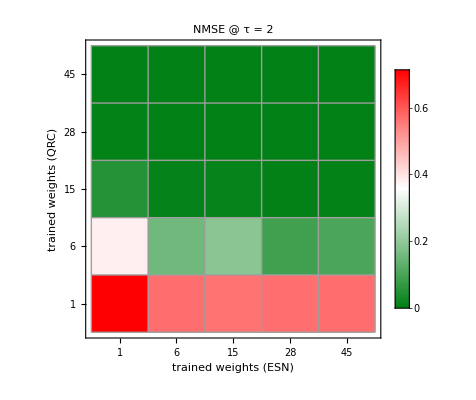

```mathematica
plotmedianresultsTr=ArrayPlot[listmedianresultsTr,ImageSize->400,AspectRatio->1,LabelStyle->15,PlotLegends->Automatic,FrameLabel->{"trained weights (QRC)","trained weights (ESN)"},ColorFunctionScaling->True,ColorFunction->Function[x,ColorDataFunction[…][1-x]],PlotLabel->"NMSE @ τ = "<>ToString[delay],FrameTicks->{{ticks,None},{ticks,None}},Mesh->True,Frame->True(*,DataRange->{MinMax[listτ],MinMax[listn]}*),DataReversed->True]
```

```mathematica
plotmedianresultsTr=ArrayPlot[listmedianresultsTr,ImageSize->400,AspectRatio->1,LabelStyle->15,PlotLegends->Automatic,FrameLabel->{"trained weights (QRC)","trained weights (ESN)"},ColorFunctionScaling->True,ColorFunction->Function[x,GrayLevel[x]],PlotLabel->"NMSE @ τ = "<>ToString[delay],FrameTicks->{{ticks,None},{ticks,None}},Mesh->True,Frame->True(*,DataRange->{MinMax[listτ],MinMax[listn]}*),DataReversed->True]
```

-Graphics-

### Show plots

```mathematica
plotmedianresultsTr
```

-Graphics-

```mathematica
AbsoluteTime[]-time
```

24.753308

## Determinant task, random ensemble, fixed delay handled equally as the sizes are varied

```mathematica
time=AbsoluteTime[];
seed=1247;
```

### Generate the task

#### Parameters for the task

```mathematica
{prep,train,test}={500,3000,1000};
delay=2;
```

#### The task proper

```mathematica
{getrandominput,gettarget,figureofmerit}=makeElementTask[];
getfinaltarget=makeDetTask[][[2]];
```

### Parameters for the RC

#### Parameters for the QHON RC (bare frequency as in task)

```mathematica
listn=Range[1,9,2];
bigR=0.4;
p=7./9;
bigM=100000;
```

#### Parameters for the ESN RC

```mathematica
listnESN=(listn^2-listn)/2+listn;
ρ0=0.1; 
ι0=0.01;
pESN=1.;
spatESN=1;
myafun={Tanh(*Tanh*),Ramp(*ReLu*),Function[x,Ramp[x]-0.01Ramp[-x]](*leaky ReLu*),Function[x,x](*identity (linear ESN)*),Function[x,Log[1.+Exp[x]]](*softmax*)}[[-1]];
```

### Computations

```mathematica
SeedRandom[seed];
listparallelseeds=RandomInteger[1*^6{-1,1},$KernelCount];
ParallelEvaluate[SeedRandom[listparallelseeds[[$KernelID]]]];
```

```mathematica
done=0;SetSharedVariable[done]
```

```mathematica
Monitor[listresults=ParallelTable[
(*random input*)
listinput=getrandominput[prep+train+test];
(*all targets for this delay*)
listtargetQ={
gettarget[listinput,1,1,Ceiling[delay/2]]//Function[listtarget,listtarget-Mean[listtarget]],
gettarget[listinput,1,2,Ceiling[delay/2]]//Function[listtarget,listtarget-Mean[listtarget]],
gettarget[listinput,2,2,Ceiling[delay/2]]//Function[listtarget,listtarget-Mean[listtarget]]
};
listtargetC={getfinaltarget[listinput,delay]//Function[listtarget,listtarget-Mean[listtarget]]};
(*call hybridtrainertester*)
{NMSEofSandwich,getoutputSandwich}=hybridtrainertester[listinput,
makerandomJorgeQRCforQinput[n,bigR,p,bigM](*random Jorge QRC instance*),
makerandomESNcoerced[nESN,ρ0,ι0,myafun,pESN,spatESN,Length[listtargetQ]](*random Jorge QRC instance*),
listtargetQ,listtargetC,prep,train,test][[1,1]];
(*increment done*)
done+=1;
(*the final NMSEs*)
NMSEofSandwich,
{reps},{n,listn},{nESN,listnESN}],ProgressIndicator[done,{0,reps Length[listn]^2}]];
```

```mathematica
(listmedianresultsDet=Transpose[listresults,{3,1,2}]//Map[Median,#,{2}]&)//MatrixForm
```

(0.8518 | 0.697753 | 0.686442 | 0.690649 | 0.69493
0.789316 | 0.480519 | 0.347089 | 0.266645 | 0.251156
0.364263 | 0.32519 | 0.284528 | 0.149704 | 0.0857079
0.333158 | 0.327216 | 0.272283 | 0.0878844 | 0.0162488
0.331766 | 0.335165 | 0.276858 | 0.0619527 | 0.00765304)

### Make some plots

```mathematica
labels=listnESN;
ticks=Transpose[{Range[Length[labels]],labels}];
```

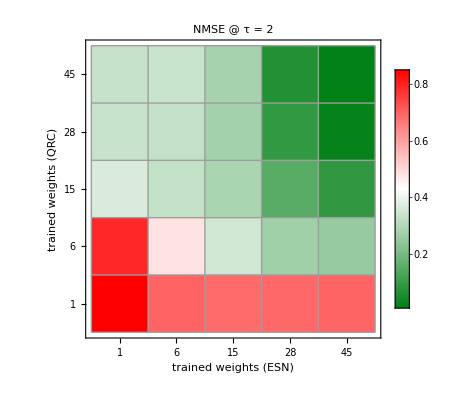

```mathematica
plotmedianresultsDet=ArrayPlot[listmedianresultsDet,ImageSize->400,AspectRatio->1,LabelStyle->15,PlotLegends->Automatic,FrameLabel->{"trained weights (QRC)","trained weights (ESN)"},ColorFunctionScaling->True,ColorFunction->Function[x,ColorDataFunction[…][1-x]],PlotLabel->"NMSE @ τ = "<>ToString[delay],FrameTicks->{{ticks,None},{ticks,None}},Mesh->True,Frame->True(*,DataRange->{MinMax[listτ],MinMax[listn]}*),DataReversed->True]
```

```mathematica
plotmedianresultsDet=ArrayPlot[listmedianresultsDet,ImageSize->400,AspectRatio->1,LabelStyle->15,PlotLegends->Automatic,FrameLabel->{"trained weights (QRC)","trained weights (ESN)"},ColorFunctionScaling->True,ColorFunction->Function[x,GrayLevel[x]],PlotLabel->"NMSE @ τ = "<>ToString[delay],FrameTicks->{{ticks,None},{ticks,None}},Mesh->True,Frame->True(*,DataRange->{MinMax[listτ],MinMax[listn]}*),DataReversed->True]
```

-Graphics-

### Show plots

```mathematica
plotmedianresultsDet
```

-Graphics-

```mathematica
AbsoluteTime[]-time
```

25.110864

## State probing task, random ensemble, fixed delay handled equally as the sizes are varied

```mathematica
time=AbsoluteTime[];
seed=1247;
```

### Generate the task

#### Parameters for the task

```mathematica
{prep,train,test}={500,3000,1000};
delay=2;
```

#### The task proper

```mathematica
{getrandominput,gettarget,figureofmerit}=makeElementTask[];
```

### Parameters for the RC

#### Parameters for the QHON RC (bare frequency as in task)

```mathematica
listn=Range[1,9,2];
bigR=0.4;
p=7./9;
bigM=100000;
```

#### Parameters for the ESN RC

```mathematica
listnESN=(listn^2-listn)/2+listn;
ρ0=0.7; 
ι0=Power[10.,-4/3]; 
pESN=1.;
spatESN=1;
myafun={Tanh(*Tanh*),Ramp(*ReLu*),Function[x,Ramp[x]-0.01Ramp[-x]](*leaky ReLu*),Function[x,x](*identity (linear ESN)*),Function[x,Log[1.+Exp[x]]](*softmax*)}[[-1]];
```

### Computations

```mathematica
SeedRandom[seed];
listparallelseeds=RandomInteger[1*^6{-1,1},$KernelCount];
ParallelEvaluate[SeedRandom[listparallelseeds[[$KernelID]]]];
```

```mathematica
done=0;SetSharedVariable[done]
```

```mathematica
Monitor[listresults=ParallelTable[
(*random input*)
listinput=getrandominput[prep+train+test];
(*all targets for this delay*)
listtargetQ={
gettarget[listinput,1,1,Ceiling[delay/2]],
gettarget[listinput,1,2,Ceiling[delay/2]],
gettarget[listinput,2,2,Ceiling[delay/2]]
};
listtargetC={
gettarget[listinput,1,1,delay],
gettarget[listinput,1,2,delay],
gettarget[listinput,2,2,delay]
};
(*call hybridtrainertester*)
{listNMSEsAndgetoutputs,listobservablesSandwich}=hybridtrainertester[listinput,
makerandomJorgeQRCforQinput[n,bigR,p,bigM](*random Jorge QRC instance*),
makerandomESNcoerced[nESN,ρ0,ι0,myafun,pESN,spatESN,Length[listtargetQ]](*random Jorge QRC instance*),
listtargetQ,listtargetC,prep,train,test];
listgetoutputs=listNMSEsAndgetoutputs[[All,2]];
(*put the states together to compute the final figure of merit, the mean fidelity*)
listoutputtest=Transpose[({{listgetoutputs[[1]][listobservablesSandwich[[prep+train+1;;]]], listgetoutputs[[2]][listobservablesSandwich[[prep+train+1;;]]]}, {listgetoutputs[[2]][listobservablesSandwich[[prep+train+1;;]]], listgetoutputs[[3]][listobservablesSandwich[[prep+train+1;;]]]}}),{2,3,1}];
listtargettest=Transpose[({{listtargetC[[1,prep+train+1;;]], listtargetC[[2,prep+train+1;;]]}, {listtargetC[[2,prep+train+1;;]], listtargetC[[3,prep+train+1;;]]}}),{2,3,1}];
listfidelity=MapThread[fidelitypurestatesQuadratures,{listoutputtest,listtargettest}];
listfidelitygoodcases=Select[listfidelity,(#∈Reals&&0≤#≤1)&];
(*increment done*)
done+=1;
(*finally!*)
Mean@listfidelitygoodcases,
{reps},{n,listn},{nESN,listnESN}],ProgressIndicator[done,{0,reps Length[listn]^2}]];
```

```mathematica
(listmedianresultsState=Transpose[listresults,{3,1,2}]//Map[Median,#,{2}]&)//MatrixForm
```

(0.775873 | 0.810597 | 0.82196 | 0.818262 | 0.820702
0.797044 | 0.841906 | 0.927392 | 0.936396 | 0.961657
0.914225 | 0.950066 | 0.977255 | 0.983423 | 0.989369
0.967409 | 0.983776 | 0.992742 | 0.996106 | 0.997888
0.991141 | 0.993348 | 0.996516 | 0.998175 | 0.999082)

### Make some plots

```mathematica
labels=listnESN;
ticks=Transpose[{Range[Length[labels]],labels}];
```

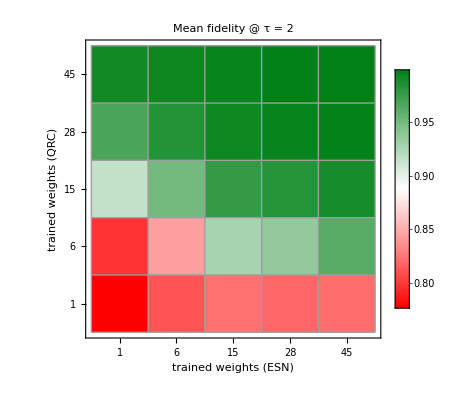

```mathematica
plotmedianresultsState=ArrayPlot[listmedianresultsState,ImageSize->400,AspectRatio->1,LabelStyle->15,FrameLabel->{"trained weights (QRC)","trained weights (ESN)"},ColorFunctionScaling->True,ColorFunction->"RedGreenSplit",PlotLabel->"Mean fidelity @ τ = "<>ToString[delay],FrameTicks->{{ticks,None},{ticks,None}},Mesh->True,Frame->True(*,DataRange->{MinMax[listτ],MinMax[listn]}*),DataReversed->True,PlotLegends->Automatic]
```

```mathematica
plotmedianresultsState=ArrayPlot[listmedianresultsState,ImageSize->400,AspectRatio->1,LabelStyle->15,FrameLabel->{"trained weights (QRC)","trained weights (ESN)"},ColorFunctionScaling->True,ColorFunction->Function[x,GrayLevel[1-x]],PlotLabel->"Mean fidelity @ τ = "<>ToString[delay],FrameTicks->{{ticks,None},{ticks,None}},Mesh->True,Frame->True(*,DataRange->{MinMax[listτ],MinMax[listn]}*),DataReversed->True,PlotLegends->Automatic]
```

-Graphics-

### Show plots

```mathematica
plotmedianresultsState
```

-Graphics-

```mathematica
AbsoluteTime[]-time
```

25.933438

## Entanglement detection task, random ensemble, 2 mode squeezed thermal state, Ramp off-loaded, multiple delays divided ceiling and floor half

```mathematica
time=AbsoluteTime[];
seed=1247;
```

### Generate the task

#### Parameters for the task

```mathematica
{prep,train,test}={500,3000,1000};
(*seed=4011;*)
delay=2;
```

#### The task proper

A bit rough but okay.

```mathematica
(*create inputs and target*)
SeedRandom[seed];
gettarget=makeElementTask[][[2]];
```

### Parameters for the RC

#### Parameters for the QHON RC (bare frequency as in task)

```mathematica
listn=Range[1,9,2];
bigR=0.4;
p=7./9;
bigM=100000;
```

#### Parameters for the ESN RC

```mathematica
listnESN=(listn^2-listn)/2+listn;
ρ0=0.1; 
ι0=0.01;
pESN=1.;
spatESN=1;
myafun={Tanh(*Tanh*),Ramp(*ReLu*),Function[x,Ramp[x]-0.01Ramp[-x]](*leaky ReLu*),Function[x,x](*identity (linear ESN)*),Function[x,Log[1.+Exp[x]]](*softmax*)}[[-1]];
```

### Computations

```mathematica
SeedRandom[seed];
listparallelseeds=RandomInteger[1*^6{-1,1},$KernelCount];
ParallelEvaluate[SeedRandom[listparallelseeds[[$KernelID]]]];
```

```mathematica
done=0;SetSharedVariable[done]
```

```mathematica
Monitor[listresults=ParallelTable[
(*random input*)
list2moder=RandomReal[{0.,0.75},prep+train+test];
listnth=RandomReal[{0.,1.25},prep+train+test];
listinput=getσSTSQuadratures@@@({listnth,list2moder}ᵀ);
(*all targets for this delay*)
listtargetQ={
gettarget[listinput,1,1,Ceiling[delay/2]],
gettarget[listinput,1,3,Ceiling[delay/2]],
gettarget[listinput,2,4,Ceiling[delay/2]]
};
listtargetC={(2RotateRight[list2moder,delay]-Log[1+2RotateRight[listnth,delay]])/Log[2]};
(*ramp-less!*)
listfinaltarget=RotateRight[loganegaQuadratures[listinput],delay];
(*call hybridtrainertester*)
{listNMSEsAndgetoutputs,listobservablesSandwich}=hybridtrainertester[listinput,
ReplacePart[makerandomJorgeQRCforQinput[n,bigR,p,bigM],3-> gettwomodepreprocess[n]](*random Jorge QRC instance, with two mode preprocess*),
makerandomESNcoerced[nESN,ρ0,ι0,myafun,pESN,spatESN,Length[listtargetQ]](*random Jorge QRC instance*),
listtargetQ,listtargetC,prep,train,test];
getoutputSandwich=listNMSEsAndgetoutputs[[1,2]];
(*we Ramp separately*)
(*if you want, you can think of it as a single Relu*)
listoutputfinal=Ramp[getoutputSandwich[listobservablesSandwich]];
mean=listfinaltarget[[prep+train+1;;]]//Mean;
(*increment done*)
done+=1;
(*the final NMSEs*)
getNMSE[listoutputfinal[[prep+train+1;;]]-mean,listfinaltarget[[prep+train+1;;]]-mean],
{reps},{n,listn},{nESN,listnESN}],ProgressIndicator[done,{0,reps Length[listn]^2}]];
```

```mathematica
(listmedianresultsloganega=Transpose[listresults,{3,1,2}]//Map[Median,#,{2}]&)//MatrixForm
```

(1.45604 | 1.45924 | 1.43999 | 1.46269 | 1.4209
0.771635 | 0.322284 | 0.28311 | 0.223459 | 0.139046
0.220019 | 0.177507 | 0.150516 | 0.0675645 | 0.0620969
0.221653 | 0.162215 | 0.0995387 | 0.0413555 | 0.0441032
0.172026 | 0.159159 | 0.0879116 | 0.0371375 | 0.0373463)

### Make some plots

```mathematica
labels=listnESN;
ticks=Transpose[{Range[Length[labels]],labels}];
```

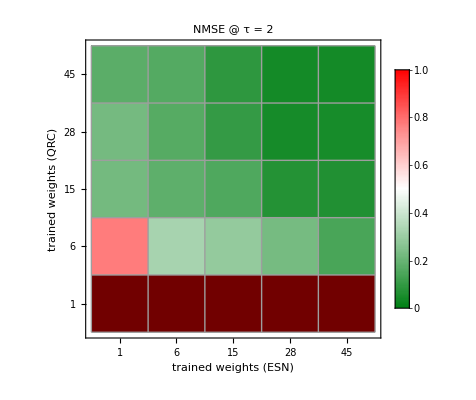

```mathematica
plotmedianresultsloganega=ArrayPlot[listmedianresultsloganega,ImageSize->400,AspectRatio->1,LabelStyle->15,PlotLegends->Automatic,FrameLabel->{"trained weights (QRC)","trained weights (ESN)"},ColorFunctionScaling->True,ColorFunction->Function[x,ColorDataFunction[…][1-x]],PlotLabel->"NMSE @ τ = "<>ToString[delay],FrameTicks->{{ticks,None},{ticks,None}},Mesh->True,Frame->True(*,DataRange->{MinMax[listτ],MinMax[listn]}*),DataReversed->True,PlotRange->{0,1},ClippingStyle->Darker@Darker@Red]
```

```mathematica
plotmedianresultsloganega=ArrayPlot[listmedianresultsloganega,ImageSize->400,AspectRatio->1,LabelStyle->15,PlotLegends->Automatic,FrameLabel->{"trained weights (QRC)","trained weights (ESN)"},ColorFunctionScaling->True,ColorFunction->Function[x,GrayLevel[x]],PlotLabel->"NMSE @ τ = "<>ToString[delay],FrameTicks->{{ticks,None},{ticks,None}},Mesh->True,Frame->True(*,DataRange->{MinMax[listτ],MinMax[listn]}*),DataReversed->True,PlotRange->{0,1},ClippingStyle->White]
```

-Graphics-

### Show plots

```mathematica
plotmedianresultsloganega
```

-Graphics-

```mathematica
AbsoluteTime[]-time
```

27.915743

## Combination plot

### Arrays

```mathematica
labels=listnESN;
ticks=Transpose[{Range[Length[labels]],labels}];
```

```mathematica
With[
{
cases=All,
cf=Function[x,GrayLevel[x]],
delay=2
},
With[
{
ticks=Transpose[{Range[Length[labels[[cases]]]],labels[[cases]]}]
},
plotTr=ArrayPlot[listmedianresultsTr[[cases,cases]],ImageSize->250,AspectRatio->1,LabelStyle->15,PlotLegends->Placed[BarLegend[{cf,MinMax[listmedianresultsTr[[cases,cases]]]},LegendLabel->"NMSE of shifted Tr(σ) @ τ = "<>ToString[delay],LegendMarkerSize->205],Top],FrameLabel->{"trained weights (QRC)",None},ColorFunctionScaling->True,ColorFunction->cf,FrameTicks->{{ticks,None},{None,None}},Mesh->True,Frame->True(*,DataRange->{MinMax[listτ],MinMax[listn]}*),DataReversed->True]
]
]
```

-Graphics-

```mathematica
With[
{
cases=All,
cf=Function[x,GrayLevel[x]],
delay=2
},
With[
{
ticks=Transpose[{Range[Length[labels[[cases]]]],labels[[cases]]}]
},
plotDet=ArrayPlot[listmedianresultsDet[[cases,cases]],ImageSize->205,AspectRatio->1,LabelStyle->15,PlotLegends->Placed[BarLegend[{cf,MinMax[listmedianresultsDet[[cases,cases]]]},LegendLabel->"NMSE of shifted Det(σ) @ τ = "<>ToString[delay]],Top],FrameLabel->{None,None},ColorFunctionScaling->True,ColorFunction->cf,FrameTicks->{{None,None},{None,None}},Mesh->True,Frame->True(*,DataRange->{MinMax[listτ],MinMax[listn]}*),DataReversed->True]
]
]
```

-Graphics-

```mathematica
With[
{
cases=All,
cf=Function[x,GrayLevel[x]],
delay=2
},
With[
{
ticks=Transpose[{Range[Length[labels[[cases]]]],labels[[cases]]}]
},
plotState=ArrayPlot[1-listmedianresultsState[[cases,cases]],ImageSize->250,AspectRatio->1,LabelStyle->15,PlotLegends->Placed[BarLegend[{cf,MinMax[1-listmedianresultsState[[cases,cases]]]},LegendLabel->Placed["1 - F @ τ = "<>ToString[delay],Bottom],LegendMarkerSize->205],Bottom],FrameLabel->{"trained weights (QRC)","trained weights (ESN)"},ColorFunctionScaling->True,ColorFunction->cf,FrameTicks->{{ticks,None},{ticks,None}},Mesh->True,Frame->True(*,DataRange->{MinMax[listτ],MinMax[listn]}*),DataReversed->True]
]
]
```

-Graphics-

```mathematica
With[
{
cases=All,
cf=Function[x,GrayLevel[x]],
delay=2
},
With[
{
ticks=Transpose[{Range[Length[labels[[cases]]]],labels[[cases]]}]
},
plotloganega=ArrayPlot[listmedianresultsloganega[[cases,cases]],ImageSize->205,AspectRatio->1,LabelStyle->15,PlotLegends->Placed[BarLegend[{cf,{Min[listmedianresultsloganega[[cases,cases]]],(Clip[listmedianresultsloganega[[cases,cases]]]//Flatten//Tally)[[2,1]]}},LegendLabel->Placed["NMSE of shifted E(σ) @ τ = "<>ToString[delay],Bottom]],Bottom],FrameLabel->{None,"trained weights (ESN)"},ColorFunctionScaling->True,ColorFunction->cf,FrameTicks->{{None,None},{ticks,None}},Mesh->True,Frame->True(*,DataRange->{MinMax[listτ],MinMax[listn]}*),DataReversed->True,PlotRange->{0,1},ClippingStyle->White]
]
]
```

-Graphics-

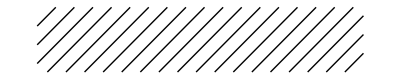

```mathematica
hatches=
With[
{
δ=0.01
},
ParametricPlot[{x,y},{x,y}∈Rectangle[{0,0}+δ,{5,1}-δ],Mesh->20,MeshFunctions->{#1-#2&},MeshStyle->Black,BoundaryStyle->None,PlotStyle->None,Axes->False,Frame->False]
]
```

```mathematica
plotloganegahatched=Show[{plotloganega,hatches}]
```

-Graphics-

### Combo

```mathematica
plotlattices=Grid[{
{plotTr,plotDet},
{plotState,plotloganegahatched}
},
Spacings->{0.,0.}]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

Fig. 4, shallow non-hybrid benchmarks

## Trace task

```mathematica
seed=12047;
```

### Generate the task

#### Parameters for the task

```mathematica
{prep,train,test}={500,3000,1000};
listτ=Range[0,5];
```

#### The task proper

```mathematica
{getrandominput,gettarget,figureofmerit}=makeTraceTask[];
```

### Parameters for the RC

#### Parameters for the Q reservoir

```mathematica
n=9;
bigR=0.4;
p=7./9;
bigM=100000;
```

#### Parameters for the ESN RC

```mathematica
nESN=(n^2-n)/2+n;
ρ0=0.7; 
ι0=Power[10.,-4/3]; 
pESN=1.;
spatESN=1;
myafun={Tanh(*Tanh*),Ramp(*ReLu*),Function[x,Ramp[x]-0.01Ramp[-x]](*leaky ReLu*),Function[x,x](*identity (linear ESN)*),Function[x,Log[1.+Exp[x]]](*softmax*)}[[-1]];
```

### Computations

```mathematica
SeedRandom[seed];
Quiet@LaunchKernels[$ProcessorCount-$KernelCount];
listparallelseeds=RandomInteger[1*^6{-1,1},$KernelCount];
ParallelEvaluate[SeedRandom[listparallelseeds[[$KernelID]]]];
```

#### For the hybrid system

```mathematica
done=0;SetSharedVariable[done]
```

```mathematica
Monitor[listresultsTrHybridNew=ParallelTable[
(*random input*)
listinput=getrandominput[prep+train+test];
(*all targets for this delay*)
listtargetQ={gettarget[listinput,0]//Function[listtarget,listtarget-Mean[listtarget]]};
listtargetC={gettarget[listinput,delay]//Function[listtarget,listtarget-Mean[listtarget]]};
(*call hybridtrainertester*)
{NMSEofSandwich,getoutputSandwich}=hybridtrainertester[listinput,
makerandomJorgeQRCforQinput[n,bigR,p,bigM](*random Jorge QRC instance*),
makerandomESNcoerced[nESN,ρ0,ι0,myafun,pESN,spatESN,Length[listtargetQ]](*random Jorge QRC instance*),
listtargetQ,listtargetC,prep,train,test][[1,1]];
(*increment done*)
done+=1;
(*the final NMSEs*)
NMSEofSandwich,
{reps},{delay,listτ}]ᵀ,ProgressIndicator[done,{0,reps Length[listτ]}]]//AbsoluteTiming//First
```

8.52888

#### ESN only: the input size is as before and we just feed it directly to the ESN

```mathematica
done=0;SetSharedVariable[done]
```

```mathematica
preprocess=makerandomJorgeQRCforQinput[n,bigR,p,bigM][[3]];
homodyne=getESNonlyreadoutQuadraturesM[n,bigM];
```

```mathematica
Monitor[listresultsTrESN=ParallelTable[
listinput=getrandominput[prep+train+test];
(*all targets for this delay*)
listtargetC=gettarget[listinput,delay]//Function[listtarget,listtarget-Mean[listtarget]];
(*create an ESN instance, larger size to account for the missing QRC*)
{updateESN,getrandominitESN,preprocessESN,readoutESN}=makerandomESNcoerced[2 nESN,ρ0,ι0,myafun,pESN,spatESN,nESN];
(*feed the homodyned input directly to the ESN*)
listinputESN=listinput//preprocess//homodyne;
(*get the ESN observables*)
listobservablesESN=getobservables[updateESN,getrandominitESN[],preprocessESN,listinputESN,readoutESN];
(*increment done*)
done+=1;
(*train & test to get the NMSE*)
First@trainertester[listobservablesESN,listtargetC,prep,train,test],
{reps},{delay,listτ}]ᵀ,ProgressIndicator[done,{0,reps Length[listτ]}]]//AbsoluteTiming//First
```

7.47654

#### QRC only: just skip the ESN! But make the QRC bigger

```mathematica
done=0;SetSharedVariable[done]
```

```mathematica
Monitor[listresultsTrQRC=ParallelTable[
listinput=getrandominput[prep+train+test];
(*create a QRC instance*)
{update,getinit,preprocess,readout}=makerandomJorgeQRCforQinput[n,bigR,p,bigM];
(*get the observables, sampling noise taken care of by readout*)
listobservablesA=getobservables[update,getinit[],preprocess,listinput,readout];
(*create another QRC instance*)
{update,getinit,preprocess,readout}=makerandomJorgeQRCforQinput[n,bigR,p,bigM];
(*get the observables, sampling noise taken care of by readout*)
listobservablesB=getobservables[update,getinit[],preprocess,listinput,readout];
(*all targets for this delay*)
listtargetQ=gettarget[listinput,delay]//Function[listtarget,listtarget-Mean[listtarget]];
(*increment done*)
done+=1;
(*call trainertester*)
First@trainertester[Join[listobservablesA,listobservablesB,2],listtargetQ,prep,train,test],
{reps},{delay,listτ}]ᵀ,ProgressIndicator[done,{0,reps Length[listτ]}]]//AbsoluteTiming//First
```

16.3948

### Make some plots

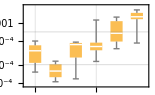

```mathematica
With[
{
tickticks={0.0002,0.0007,0.0024}
},
With[
{
verticalticks=({tickticks,ToString/@(NumberForm[#,{2,4}]&/@tickticks)}ᵀ),
gridlines=GridLines->{Automatic,Log@tickticks}
},
miniplotTrD=BoxWhiskerChart[listresultsTrHybridNew,ImageSize->155,LabelStyle->Automatic,gridlines,Frame->True,FrameTicks->{{verticalticks,Automatic},{Automatic,None}},Ticks->None,ChartStyle->Directive[RGBColor[0.982864, 0.7431472, 0.3262672],Opacity[1]],PlotRange->All,ScalingFunctions->"Log",ChartLabels->listτ]//Framed[#,RoundingRadius->5,Background->White,FrameStyle->Thin]&
]
]
```

```mathematica
plotresultsTrDNew=ListLogPlot[
{listresultsTrHybridNew,listresultsTrQRC,listresultsTrESN}//Map[Map[Mean]],
Joined->True,
DataRange->{0,5},
PlotStyle->(Directive[#,Thick,Opacity[1]]&/@{RGBColor[0.982864, 0.7431472, 0.3262672],RGBColor[0.784, 0.47519999999999996, 0.2],RGBColor[0.4992, 0.5552, 0.8309304]}),
PlotMarkers->{Automatic,20},
Frame->True,
GridLines->Automatic,
ImageSize->450,LabelStyle->15,
FrameLabel->{None,"shifted Tr(σ) NMSE"},
FrameTicks->{None,Automatic},
Epilog->Inset[miniplotTrD,Scaled[{0.05,0.600}],Left]
]
```

-Graphics-

### Show plots

```mathematica
plotresultsTrDNew
```

-Graphics-

## Determinant task

```mathematica
seed=192467;
```

### Generate the task

#### Parameters for the task

```mathematica
{prep,train,test}={500,3000,1000};
listτ=Range[0,5];
```

#### The task proper

```mathematica
{getrandominput,gettarget,figureofmerit}=makeElementTask[];
getfinaltarget=makeDetTask[][[2]];
```

### Parameters for the RC

#### Parameters for the Q reservoir

```mathematica
n=9;
bigR=0.4;
p=7./9;
bigM=100000;
```

#### Parameters for the ESN RC

```mathematica
nESN=(n^2-n)/2+n;
ρ0=0.1; 
ι0=0.01; 
pESN=1.;
spatESN=1;
myafun={Tanh(*Tanh*),Ramp(*ReLu*),Function[x,Ramp[x]-0.01Ramp[-x]](*leaky ReLu*),Function[x,x](*identity (linear ESN)*),Function[x,Log[1.+Exp[x]]](*softmax*)}[[-1]];
```

### Computations

```mathematica
SeedRandom[seed];
listparallelseeds=RandomInteger[1*^6{-1,1},$KernelCount];
ParallelEvaluate[SeedRandom[listparallelseeds[[$KernelID]]]];
```

#### For the hybrid system

```mathematica
done=0;SetSharedVariable[done]
```

```mathematica
Monitor[listresultsDetHybrid=ParallelTable[
(*random input*)
listinput=getrandominput[prep+train+test];
(*all targets for this delay*)
listtargetQ={
gettarget[listinput,1,1,Ceiling[delay/2]]//Function[listtarget,listtarget-Mean[listtarget]],
gettarget[listinput,1,2,Ceiling[delay/2]]//Function[listtarget,listtarget-Mean[listtarget]],
gettarget[listinput,2,2,Ceiling[delay/2]]//Function[listtarget,listtarget-Mean[listtarget]]
};
listtargetC={getfinaltarget[listinput,delay]//Function[listtarget,listtarget-Mean[listtarget]]};
(*call hybridtrainertester*)
{NMSEofSandwich,getoutputSandwich}=hybridtrainertester[listinput,
makerandomJorgeQRCforQinput[n,bigR,p,bigM](*random Jorge QRC instance*),
makerandomESNcoerced[nESN,ρ0,ι0,myafun,pESN,spatESN,Length[listtargetQ]](*random Jorge QRC instance*),
listtargetQ,listtargetC,prep,train,test][[1,1]];
(*increment done*)
done+=1;
(*the final NMSEs*)
NMSEofSandwich,
{reps},{delay,listτ}]ᵀ,ProgressIndicator[done,{0,reps Length[listτ]}]]//AbsoluteTiming//First
```

8.71761

#### ESN only: the input size is as before and we just feed it directly to the ESN

```mathematica
done=0;SetSharedVariable[done]
```

```mathematica
preprocess=makerandomJorgeQRCforQinput[n,bigR,p,bigM][[3]];
homodyne=getESNonlyreadoutQuadraturesM[n,bigM];
```

```mathematica
Monitor[listresultsDetESN=ParallelTable[
listinput=getrandominput[prep+train+test];
(*all targets for this delay*)
listtarget=getfinaltarget[listinput,delay];
shift=Mean[listtarget];
listtarget-=shift;
(*create an ESN instance, larger size to account for the missing QRC*)
{updateESN,getrandominitESN,preprocessESN,readoutESN}=makerandomESNcoerced[2 nESN,ρ0,ι0,myafun,pESN,spatESN,nESN];
(*feed the homodyned input directly to the ESN*)
listinputESN=listinput//preprocess//homodyne;
(*get the ESN observables*)
listobservablesESN=getobservables[updateESN,getrandominitESN[],preprocessESN,listinputESN,readoutESN];
(*increment done*)
done+=1;
(*train & test to get the NMSE*)
First@trainertester[listobservablesESN,listtarget,prep,train,test],
{reps},{delay,listτ}]ᵀ,ProgressIndicator[done,{0,reps Length[listτ]}]]//AbsoluteTiming//First
```

7.53246

#### QRC only: just skip the ESN! But make the QRC bigger

```mathematica
done=0;SetSharedVariable[done]
```

```mathematica
Monitor[listresultsDetQRC=ParallelTable[
listinput=getrandominput[prep+train+test];
(*create a QRC instance*)
{update,getinit,preprocess,readout}=makerandomJorgeQRCforQinput[n,bigR,p,bigM];
(*get the observables, sampling noise taken care of by readout*)
listobservablesA=getobservables[update,getinit[],preprocess,listinput,readout];
(*create another QRC instance*)
{update,getinit,preprocess,readout}=makerandomJorgeQRCforQinput[n,bigR,p,bigM];
(*get the observables, sampling noise taken care of by readout*)
listobservablesB=getobservables[update,getinit[],preprocess,listinput,readout];
(*all targets for this delay*)
listtarget=getfinaltarget[listinput,delay];
shift=Mean[listtarget];
listtarget-=shift;
(*increment done*)
done+=1;
(*call trainertester*)
First@trainertester[Join[listobservablesA,listobservablesB,2],listtarget,prep,train,test],
{reps},{delay,listτ}]ᵀ,ProgressIndicator[done,{0,reps Length[listτ]}]]//AbsoluteTiming//First
```

16.4152

### Make some plots

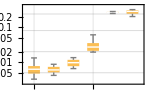

```mathematica
With[
{
tickticks={0.005,0.020,0.080,0.240}
},
With[
{
verticalticks=({tickticks,ToString/@(NumberForm[#,{3,3}]&/@tickticks)}ᵀ),
gridlines=GridLines->{Automatic,Log@tickticks}
},
miniplotDetD=BoxWhiskerChart[listresultsDetHybrid,ImageSize->150,LabelStyle->Automatic,gridlines,Frame->True,FrameTicks->{{verticalticks,Automatic},{Automatic,None}},Ticks->None,ChartStyle->Directive[RGBColor[0.982864, 0.7431472, 0.3262672],Opacity[1]],PlotRange->All,ScalingFunctions->"Log",ChartLabels->listτ]//Framed[#,RoundingRadius->5,Background->White,FrameStyle->Thin]&
]
]
```

```mathematica
plotresultsDetD=ListLogPlot[
{listresultsDetHybrid,listresultsDetQRC,listresultsDetESN}//Map[Map[Mean]],
Joined->True,
DataRange->{0,5},
PlotStyle->(Directive[#,Thick,Opacity[1]]&/@{RGBColor[0.982864, 0.7431472, 0.3262672],RGBColor[0.784, 0.47519999999999996, 0.2],RGBColor[0.4992, 0.5552, 0.8309304]}),
PlotMarkers->{Automatic,20},
Frame->True,
GridLines->Automatic,
ImageSize->450,LabelStyle->15,
FrameLabel->{None,"shifted det(σ) NMSE"},
FrameTicks->{None,Automatic},
Epilog->Inset[miniplotDetD,Scaled[{0.05,0.500}],Left],
PlotRange->{Automatic,{0.8 0.005,Automatic}}
]
```

-Graphics-

### Show plots

```mathematica
plotresultsDetD
```

-Graphics-

## State probing task

```mathematica
seed=258;
```

### Generate the task

#### Parameters for the task

```mathematica
{prep,train,test}={500,3000,1000};
listτ=Range[0,5];
```

#### The task proper

```mathematica
{getrandominput,gettarget,figureofmerit}=makeElementTask[];
```

### Parameters for the RC

#### Parameters for the Q reservoir

```mathematica
n=9;
bigR=0.4;
p=7./9;
bigM=100000;
```

#### Parameters for the ESN RC

```mathematica
nESN=(n^2-n)/2+n;
ρ0=0.7; 
ι0=Power[10.,-4/3]; 
pESN=1.;
spatESN=1;
myafun={Tanh(*Tanh*),Ramp(*ReLu*),Function[x,Ramp[x]-0.01Ramp[-x]](*leaky ReLu*),Function[x,x](*identity (linear ESN)*),Function[x,Log[1.+Exp[x]]](*softmax*)}[[-1]];
```

### Computations

```mathematica
SeedRandom[seed];
listparallelseeds=RandomInteger[1*^6{-1,1},$KernelCount];
ParallelEvaluate[SeedRandom[listparallelseeds[[$KernelID]]]];
```

#### For the hybrid system

```mathematica
done=0;SetSharedVariable[done]
```

```mathematica
Monitor[listresultsStateHybrid=ParallelTable[
(*random input*)
listinput=getrandominput[prep+train+test];
(*all targets for this delay*)
listtargetQ={
gettarget[listinput,1,1,Ceiling[delay/2]],
gettarget[listinput,1,2,Ceiling[delay/2]],
gettarget[listinput,2,2,Ceiling[delay/2]]
};
listtargetC={
gettarget[listinput,1,1,delay],
gettarget[listinput,1,2,delay],
gettarget[listinput,2,2,delay]
};
(*call hybridtrainertester*)
{listNMSEsAndgetoutputs,listobservablesSandwich}=hybridtrainertester[listinput,
makerandomJorgeQRCforQinput[n,bigR,p,bigM](*random Jorge QRC instance*),
makerandomESNcoerced[nESN,ρ0,ι0,myafun,pESN,spatESN,Length[listtargetQ]](*random Jorge QRC instance*),
listtargetQ,listtargetC,prep,train,test];
listgetoutputs=listNMSEsAndgetoutputs[[All,2]];
(*put the states together to compute the final figure of merit, the mean fidelity*)
listoutputtest=Transpose[({{listgetoutputs[[1]][listobservablesSandwich[[prep+train+1;;]]], listgetoutputs[[2]][listobservablesSandwich[[prep+train+1;;]]]}, {listgetoutputs[[2]][listobservablesSandwich[[prep+train+1;;]]], listgetoutputs[[3]][listobservablesSandwich[[prep+train+1;;]]]}}),{2,3,1}];
listtargettest=Transpose[({{listtargetC[[1,prep+train+1;;]], listtargetC[[2,prep+train+1;;]]}, {listtargetC[[2,prep+train+1;;]], listtargetC[[3,prep+train+1;;]]}}),{2,3,1}];
listfidelity=MapThread[fidelitypurestatesQuadratures,{listoutputtest,listtargettest}];
listfidelitygoodcases=Select[listfidelity,(#∈Reals&&0≤#≤1)&];
(*increment done*)
done+=1;
(*finally!*)
Mean@listfidelitygoodcases,
{reps},{delay,listτ}]ᵀ,ProgressIndicator[done,{0,reps Length[listτ]}]]//AbsoluteTiming//First
```

9.24535

#### ESN only: the input size is as before and we just feed it directly to the ESN

```mathematica
preprocess=makerandomJorgeQRCforQinput[n,bigR,p,bigM][[3]];
homodyne=getESNonlyreadoutQuadraturesM[n,bigM];
```

```mathematica
done=0;SetSharedVariable[done]
```

```mathematica
Monitor[listresultsStateESN=ParallelTable[
listinput=getrandominput[prep+train+test];
(*all targets for this delay*)
listtarget11ESN=gettarget[listinput,1,1,delay];
listtarget12ESN=gettarget[listinput,1,2,delay];
listtarget22ESN=gettarget[listinput,2,2,delay];
(*create an ESN instance, larger size to account for the missing QRC*)
{updateESN,getrandominitESN,preprocessESN,readoutESN}=makerandomESNcoerced[2 nESN,ρ0,ι0,myafun,pESN,spatESN,nESN];
(*feed the homodyned input directly to the ESN*)
listinputESN=listinput//preprocess//homodyne;
(*get the ESN observables*)
listobservablesESN=getobservables[updateESN,getrandominitESN[],preprocessESN,listinputESN,readoutESN];
(*call trainertester*)
{NMSE11,getoutput11}=trainertester[listobservablesESN,listtarget11ESN,prep,train,test];
{NMSE12,getoutput12}=trainertester[listobservablesESN,listtarget12ESN,prep,train,test];
{NMSE22,getoutput22}=trainertester[listobservablesESN,listtarget22ESN,prep,train,test];
(*put the states together to compute the final figure of merit, the mean fidelity*)
listoutputtest=Transpose[({{getoutput11[listobservablesESN[[prep+train+1;;]]], getoutput12[listobservablesESN[[prep+train+1;;]]]}, {getoutput12[listobservablesESN[[prep+train+1;;]]], getoutput22[listobservablesESN[[prep+train+1;;]]]}}),{2,3,1}];
listtargettest=Transpose[({{listtarget11ESN[[prep+train+1;;]], listtarget12ESN[[prep+train+1;;]]}, {listtarget12ESN[[prep+train+1;;]], listtarget22ESN[[prep+train+1;;]]}}),{2,3,1}];
listfidelity=MapThread[fidelitypurestatesQuadratures,{listoutputtest,listtargettest}];
listfidelitygoodcases=Select[listfidelity,(#∈Reals&&0≤#≤1)&];
(*increment done*)
done+=1;
(*finally!*)
Mean@listfidelitygoodcases,
{reps},{delay,listτ}]ᵀ,ProgressIndicator[done,{0,reps Length[listτ]}]]//AbsoluteTiming//First
```

7.93919

#### QRC only: just skip the ESN! But make the QRC bigger

```mathematica
done=0;SetSharedVariable[done]
```

```mathematica
Monitor[listresultsStateQRC=ParallelTable[
listinput=getrandominput[prep+train+test];
(*create a QRC instance*)
{update,getinit,preprocess,readout}=makerandomJorgeQRCforQinput[n,bigR,p,bigM];
(*get the observables, sampling noise taken care of by readout*)
listobservablesA=getobservables[update,getinit[],preprocess,listinput,readout];
(*create another QRC instance*)
{update,getinit,preprocess,readout}=makerandomJorgeQRCforQinput[n,bigR,p,bigM];
(*get the observables, sampling noise taken care of by readout*)
listobservablesB=getobservables[update,getinit[],preprocess,listinput,readout];
(*combine*)
listobservables=Join[listobservablesA,listobservablesB,2];
(*all targets for this delay*)
listtarget11=gettarget[listinput,1,1,delay];
listtarget12=gettarget[listinput,1,2,delay];
listtarget22=gettarget[listinput,2,2,delay];
(*call trainertester*)
{NMSE11,getoutput11}=trainertester[listobservables,listtarget11,prep,train,test];
{NMSE12,getoutput12}=trainertester[listobservables,listtarget12,prep,train,test];
{NMSE22,getoutput22}=trainertester[listobservables,listtarget22,prep,train,test];
(*put the states together to compute the final figure of merit, the mean fidelity*)
listoutputtest=Transpose[({{getoutput11[listobservables[[prep+train+1;;]]], getoutput12[listobservables[[prep+train+1;;]]]}, {getoutput12[listobservables[[prep+train+1;;]]], getoutput22[listobservables[[prep+train+1;;]]]}}),{2,3,1}];
listtargettest=Transpose[({{listtarget11[[prep+train+1;;]], listtarget12[[prep+train+1;;]]}, {listtarget12[[prep+train+1;;]], listtarget22[[prep+train+1;;]]}}),{2,3,1}];
listfidelity=MapThread[fidelitypurestatesQuadratures,{listoutputtest,listtargettest}];
listfidelitygoodcases=Select[listfidelity,(#∈Reals&&0≤#≤1)&];
(*increment done*)
done+=1;
(*finally!*)
Mean@listfidelitygoodcases,
{reps},{delay,listτ}]ᵀ,ProgressIndicator[done,{0,reps Length[listτ]}]]//AbsoluteTiming//First
```

16.7983

### Make some plots

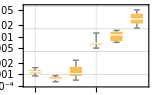

```mathematica
With[
{
tickticks={0.001,0.004,0.016,0.064}
},
With[
{
verticalticks=({tickticks,ToString/@(NumberForm[#,{3,3}]&/@tickticks)}ᵀ),
gridlines=GridLines->{Automatic,Log@tickticks}
},
miniplotStateD=BoxWhiskerChart[1-listresultsStateHybrid,ImageSize->155,LabelStyle->Automatic,gridlines,Frame->True,FrameTicks->{{verticalticks,Automatic},{Automatic,None}},Ticks->None,ChartStyle->Directive[RGBColor[0.982864, 0.7431472, 0.3262672],Opacity[1]],PlotRange->All,ScalingFunctions->"Log",ChartLabels->listτ]//Framed[#,RoundingRadius->5,Background->White,FrameStyle->Thin]&
]
]
```

```mathematica
plotresultsStateD=ListLogPlot[
{1-listresultsStateHybrid,1-listresultsStateQRC,1-listresultsStateESN}//Map[Map[Mean]],
Joined->True,
DataRange->{0,5},
PlotStyle->(Directive[#,Thick,Opacity[1]]&/@{RGBColor[0.982864, 0.7431472, 0.3262672],RGBColor[0.784, 0.47519999999999996, 0.2],RGBColor[0.4992, 0.5552, 0.8309304]}),
PlotMarkers->{Automatic,20},
Frame->True,
GridLines->Automatic,
ImageSize->450,LabelStyle->15,
FrameLabel->{"delay τ",Row@{"1-F" ,Style["(",White],"of estimated state"}},
FrameTicks->Automatic,
Epilog->Inset[miniplotStateD,Scaled[{0.05,0.600}],Left],
PlotRange->{Automatic,{5.01*^-4,0.30}}
]
```

-Graphics-

### Show plots

```mathematica
plotresultsStateD
```

-Graphics-

## Entanglement detection task

```mathematica
seed=2975;
```

### Generate the task

#### Parameters for the task

```mathematica
{prep,train,test}={500,3000,1000};
listτ=Range[0,5];
```

#### The task proper

A bit rough but okay.

```mathematica
gettarget=makeElementTask[][[2]];
```

### Parameters for the RC

#### Parameters for the Q reservoir

```mathematica
n=9;
bigR=0.4;
p=7./9;
bigM=100000;
```

#### Parameters for the ESN RC

```mathematica
nESN=(n^2-n)/2+n;
ρ0=0.1; 
ι0=0.01; 
pESN=1.;
spatESN=1;
myafun={Tanh(*Tanh*),Ramp(*ReLu*),Function[x,Ramp[x]-0.01Ramp[-x]](*leaky ReLu*),Function[x,x](*identity (linear ESN)*),Function[x,Log[1.+Exp[x]]](*softmax*)}[[-1]];
```

### Computations

```mathematica
SeedRandom[seed];
```

#### For the hybrid system

```mathematica
done=0;SetSharedVariable[done]
```

```mathematica
Monitor[listresultsloganegaHybrid=ParallelTable[
(*random input*)
list2moder=RandomReal[{0.,0.75},prep+train+test];
listnth=RandomReal[{0.,1.25},prep+train+test];
listinput=getσSTSQuadratures@@@({listnth,list2moder}ᵀ);
(*all targets for this delay*)
listtargetQ={
gettarget[listinput,1,1,Ceiling[delay/2]],
gettarget[listinput,1,3,Ceiling[delay/2]],
gettarget[listinput,2,4,Ceiling[delay/2]]
};
listtargetC={(2RotateRight[list2moder,delay]-Log[1+2RotateRight[listnth,delay]])/Log[2]};
(*ramp-less!*)
listfinaltarget=RotateRight[loganegaQuadratures[listinput],delay];
(*call hybridtrainertester*)
{listNMSEsAndgetoutputs,listobservablesSandwich}=hybridtrainertester[listinput,
ReplacePart[makerandomJorgeQRCforQinput[n,bigR,p,bigM],3-> gettwomodepreprocess[n]](*random Jorge QRC instance, with two mode preprocess*),
makerandomESNcoerced[nESN,ρ0,ι0,myafun,pESN,spatESN,Length[listtargetQ]](*random Jorge QRC instance*),
listtargetQ,listtargetC,prep,train,test];
getoutputSandwich=listNMSEsAndgetoutputs[[1,2]];
(*we Ramp separately*)
(*if you want, you can think of it as a single Relu*)
listoutputfinal=Ramp[getoutputSandwich[listobservablesSandwich]];
mean=listfinaltarget[[prep+train+1;;]]//Mean;
(*increment done*)
done+=1;
(*the final NMSEs*)
getNMSE[listoutputfinal[[prep+train+1;;]]-mean,listfinaltarget[[prep+train+1;;]]-mean],
{reps},{delay,listτ}]ᵀ,ProgressIndicator[done,{0,reps Length[listτ]}]]//AbsoluteTiming//First
```

9.51188

#### ESN only: the input size is as before and we just feed it directly to the ESN

```mathematica
done=0;SetSharedVariable[done]
```

```mathematica
preprocess2modes=gettwomodepreprocess[n];
homodyne=getESNonlyreadoutQuadraturesM[n,bigM];
```

```mathematica
Monitor[listresultsloganegaESN=ParallelTable[
(*feed the homodyned input directly to the ESN*)
listinputESN=listinput//preprocess2modes//homodyne;

listtargetESN=(2RotateRight[list2moder,delay]-Log[1+2RotateRight[listnth,delay]])/Log[2];(*ramp-less!*)
listfinaltarget=RotateRight[loganegaQuadratures[listinput],delay];
(*create an ESN instance*)
{updateESN,getrandominitESN,preprocessESN,readoutESN}=makerandomESNcoerced[2nESN,ρ0,ι0,myafun,pESN,spatESN,nESN];
(*get the ESN observables*)
listobservablesESN=getobservables[updateESN,getrandominitESN[],preprocessESN,listinputESN,readoutESN];
getoutputESN=Last@trainertester[listobservablesESN,listtargetESN,prep,train,test];
(*we Ramp separately*)
(*if you want, you can think of it as a single Relu*)
listoutputfinal=Ramp[getoutputESN[listobservablesESN]];
mean=listfinaltarget[[prep+train+1;;]]//Mean;
(*increment done*)
done+=1;
(*the final NMSEs*)
getNMSE[listoutputfinal[[prep+train+1;;]]-mean,listfinaltarget[[prep+train+1;;]]-mean],
{reps},{delay,listτ}]ᵀ,ProgressIndicator[done,{0,reps Length[listτ]}]]//AbsoluteTiming//First
```

8.08334

#### QRC only: skip the ESN

```mathematica
done=0;SetSharedVariable[done]
```

```mathematica
preprocess2modes=gettwomodepreprocess[n];
```

```mathematica
Monitor[listresultsloganegaQRC=ParallelTable[
(*create a QRC instance*)
{update,getinit,preprocess,readout}=makerandomJorgeQRCforQinput[n,bigR,p,bigM];
(*get the observables, sampling noise taken care of by readout*)
listobservablesA=getobservables[update,getinit[],preprocess2modes,listinput,readout];
(*create another QRC instance*)
{update,getinit,preprocess,readout}=makerandomJorgeQRCforQinput[n,bigR,p,bigM];
(*get the observables, sampling noise taken care of by readout*)
listobservablesB=getobservables[update,getinit[],preprocess2modes,listinput,readout];
(*combine*)
listobservables=Join[listobservablesA,listobservablesB,2];
(*all targets for this delay*)
listtargetESN=(2RotateRight[list2moder,delay]-Log[1+2RotateRight[listnth,delay]])/Log[2];(*ramp-less!*)
listfinaltarget=RotateRight[loganegaQuadratures[listinput],delay];
(*call trainertester*)
{NMSE,getoutput}=trainertester[listobservables,listtargetESN,prep,train,test];
(*we Ramp separately*)
(*if you want, you can think of it as a single Relu*)
listoutputfinal=Ramp[getoutput[listobservables]];
mean=listfinaltarget[[prep+train+1;;]]//Mean;
(*increment done*)
done+=1;
(*the final NMSEs*)
getNMSE[listoutputfinal[[prep+train+1;;]]-mean,listfinaltarget[[prep+train+1;;]]-mean],
{reps},{delay,listτ}]ᵀ,ProgressIndicator[done,{0,reps Length[listτ]}]]//AbsoluteTiming//First
```

17.4458

### Make some plots

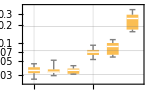

```mathematica
With[
{
tickticks={0.03,0.075,0.19,0.47}
},
With[
{
verticalticks=({tickticks,ToString/@(NumberForm[#,{3,3}]&/@tickticks)}ᵀ),
gridlines=GridLines->{Automatic,Log@tickticks}
},
miniplotloganegaD=BoxWhiskerChart[listresultsloganegaHybrid,ImageSize->150,LabelStyle->Automatic,gridlines,Frame->True,FrameTicks->{{verticalticks,Automatic},{Automatic,None}},Ticks->None,ChartStyle->Directive[RGBColor[0.982864, 0.7431472, 0.3262672],Opacity[1]],PlotRange->All,ScalingFunctions->"Log",ChartLabels->listτ]//Framed[#,RoundingRadius->5,Background->White,FrameStyle->Thin]&
]
]
```

```mathematica
format2=Replace[#,n_?(NumericQ[#]&&!Equal[#,1]&)|NumberForm[n_,_]:>NumberForm[n,{3,3}]]&;
relabel=#/.CST_Charting`ScaledTicks:>(MapAt[format2,CST[##],{All,2}]&)&;
```

```mathematica
plotresultsLoganegaD=ListLogPlot[
{listresultsloganegaHybrid,listresultsloganegaQRC,listresultsloganegaESN}//Map[Map[Mean]],
Joined->True,
DataRange->{0,5},
PlotStyle->(Directive[#,Thick,Opacity[1]]&/@{RGBColor[0.982864, 0.7431472, 0.3262672],RGBColor[0.784, 0.47519999999999996, 0.2],RGBColor[0.4992, 0.5552, 0.8309304]}),
PlotMarkers->{Automatic,20},
Frame->True,
GridLines->Automatic,
ImageSize->450,LabelStyle->15,
FrameLabel->{"delay τ","shifted E(σ) NMSE"},
FrameTicks->Automatic,
Epilog->Inset[miniplotloganegaD,Scaled[{0.05,0.7500}],Left]
]//relabel
```

-Graphics-

### Show plots

```mathematica
plotresultsLoganegaD
```

-Graphics-

## Combination plot

### Boxwhisker

```mathematica
With[
{
offset={-1.0,0},
whiskerwidth=0.25,
boxwidth=0.5,
vertlineheight=1,
boxheight=0.95,
lblnudge=0.1,
fontsize=12,
font="Helvetica",
imgsize=95
},
With[
{
min=Text[Style["min",fontsize,FontFamily->font],{boxwidth+lblnudge,0},offset],
max=Text[Style["max",fontsize,FontFamily->font],{boxwidth+lblnudge,2vertlineheight+2boxheight},offset],
firstquartile=Text[Style["1st quartile",fontsize,FontFamily->font],{boxwidth+lblnudge,vertlineheight},offset],
median=Text[Style["median",fontsize,FontFamily->font],{boxwidth+lblnudge,vertlineheight+boxheight},offset],
thirdquartile=Text[Style["3rd quartile",fontsize,FontFamily->font],{boxwidth+lblnudge,vertlineheight+2boxheight},offset]
},
With[
{
minline=Line[{{-whiskerwidth,0},{whiskerwidth,0}}],
firstverticalline=Line[{{0,0},{0,vertlineheight}}],
firstbox=Rectangle[{-boxwidth,vertlineheight},{boxwidth,vertlineheight+boxheight}],
medianline=Line[{{-boxwidth,vertlineheight+boxheight},{boxwidth,vertlineheight+boxheight}}],
lastbox=Rectangle[{-boxwidth,vertlineheight+boxheight},{boxwidth,vertlineheight+2boxheight}],
lastverticalline=Line[{{0,vertlineheight+2boxheight},{0,2vertlineheight+2boxheight}}],
maxline=Line[{{-whiskerwidth,2vertlineheight+2boxheight},{whiskerwidth,2vertlineheight+2boxheight}}]
},
With[
{
boxwhisker={minline,firstverticalline,{RGBColor[0.982864, 0.7431472, 0.3262672],firstbox},{Directive[White,Thick],medianline},lastverticalline,{RGBColor[0.982864, 0.7431472, 0.3262672],lastbox},maxline},
text={min,max,median,firstquartile,thirdquartile}
},
bw=Graphics[{boxwhisker,text},ImageSize->imgsize]
]
]
]
]
```

-Graphics-

### Else

```mathematica
LineLegend[{RGBColor[0.982864, 0.7431472, 0.3262672],RGBColor[0.784, 0.47519999999999996, 0.2],RGBColor[0.4992, 0.5552, 0.8309304]},{Style["Hybrid",15],Style["Bigger QRC",15],Style["Bigger ESN",15]},LegendMarkers->(Style[#,20]&/@{"●","■","◆"}),LegendMarkerSize->{{25,20}}]
```

```mathematica
legends=Grid[{
{Rotate[Style["Hybrid",12,FontFamily->"Helvetica"],Pi/2],bw},
{
LineLegend[{RGBColor[0.982864, 0.7431472, 0.3262672],RGBColor[0.784, 0.47519999999999996, 0.2],RGBColor[0.4992, 0.5552, 0.8309304]},{Style["Hybrid",15],Style["Bigger QRC",15],Style["Bigger ESN",15]},LegendMarkers->(Style[#,20]&/@{"●","■","◆"}),LegendMarkerSize->{{25,20}}],SpanFromLeft
}
},
Alignment->Left,
Spacings->{0.5,1.5}]
```

Hybrid | -Graphics-
 |

```mathematica
plotlineresultsD=Legended[
Grid[{
{plotresultsTrDNew,plotresultsDetD},
{plotresultsStateD,plotresultsLoganegaD}
},
Spacings->{1.5,-0.039}],
Placed[legends,Right]];
```

### Show the plot

```mathematica
plotlineresultsD
```

-Graphics-

Fig. 5, optimization of reflectivity R and sparsity p

```mathematica
seed=192467;
```

```mathematica
figRptime=AbsoluteTime[];
```

### Generate the task

#### Parameters for the task

```mathematica
{prep,train,test}={500,3000,1000};
listτ=Range[0,3];
```

#### The task proper

```mathematica
{getrandominput,gettarget,figureofmerit}=makeElementTask[];
getfinaltarget=makeDetTask[][[2]];
```

### Parameters for the RC

#### Parameters for the Q reservoir

```mathematica
n=9;
listp=Range[1./9,1,1/9];
listbigR=Range[0.1,0.9,0.1];
bigM=100000;
```

#### Parameters for the ESN

```mathematica
nESN=(n^2-n)/2+n;
ρ0=0.5; 
ι0=0.1; 
pESN=1.;
spatESN=1;
myafun={Tanh(*Tanh*),Ramp(*ReLu*),Function[x,Ramp[x]-0.01Ramp[-x]](*leaky ReLu*),Function[x,x](*identity (linear ESN)*),Function[x,Log[1.+Exp[x]]](*softmax*)}[[-1]];
```

### Computations

```mathematica
SeedRandom[seed];
```

```mathematica
done=0;SetSharedVariable[done]
```

```mathematica
Monitor[listresultsBenchMp12=ParallelTable[
listinput=getrandominput[prep+train+test];
(*create a QRC instance*)
{update,getinit,preprocess,readout}=makerandomJorgeQRCforQinput[n,bigR,p,bigM];
(*get the observables*)
listobservables=getobservables[update,getinit[],preprocess,listinput,readout];
(*all targets for this delay*)
listtarget12=gettarget[listinput,1,2,delay]//Function[listtarget,listtarget-Mean[listtarget]];
(*call trainertester*)
NMSE12=First@trainertester[listobservables,listtarget12,prep,train,test];
(*increment done*)
done+=1;
(*the final NMSEs*)
NMSE12,{reps},{delay,listτ},{p,listp},{bigR,listbigR}
],ProgressIndicator[done,{0,reps Length[listτ]Length[listp] Length[listbigR]}]];//AbsoluteTiming//First
```

424.64

### Make some plots

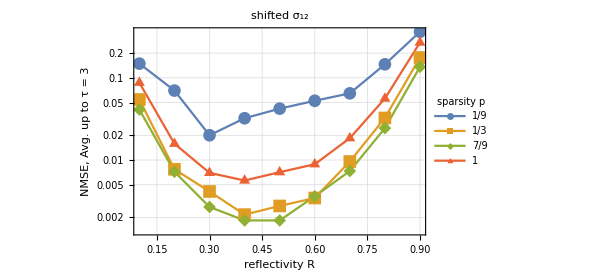

```mathematica
With[
{
delayupto=4
},
With[
{
listresultsBenchMp2D12=listresultsBenchMp12[[All,;;delayupto]]ᵀ//Mean//Mean,
pchoice={1,3,7,-1}
},
plotRp=ListLogPlot[
{listbigR,#}ᵀ&/@listresultsBenchMp2D12[[pchoice]],
Joined->True,
Frame->True,
ImageSize->450,LabelStyle->15,
GridLines->Automatic,
PlotLegends->PointLegend[{"1/9","2/9","1/3","4/9","5/9","2/3","7/9","8/9","1"}[[pchoice]],LegendLabel->"sparsity p"],
PlotLabel->"shifted σ_12",
FrameLabel->{"reflectivity R","NMSE, Avg. up to τ = "<>ToString[listτ[[delayupto]]]},
PlotRange->All,
PlotMarkers->{Automatic,13}
]
]
]
```

### Show plots

```mathematica
plotRp
```

-Graphics-

```mathematica
AbsoluteTime[]-figRptime
```

425.0447033

Fig. 6, effect of delay split

## Trace

```mathematica
seed=12047;
```

### Generate the task

#### Parameters for the task

```mathematica
{prep,train,test}={500,3000,1000};
listτ=Range[0,10];
```

#### The task proper

```mathematica
{getrandominput,gettarget,figureofmerit}=makeTraceTask[];
```

### Parameters for the RC

#### Parameters for the Q reservoir

```mathematica
n=9;
bigR=0.4;
p=7./9;
bigM=100000;
```

```mathematica
listτsplit={0.,0.5,1.}
```

{0.,0.5,1.}

#### Parameters for the ESN RC

```mathematica
nESN=(n^2-n)/2+n;
ρ0=0.7; 
ι0=Power[10.,-4/3]; 
pESN=1.;
spatESN=1;
myafun={Tanh(*Tanh*),Ramp(*ReLu*),Function[x,Ramp[x]-0.01Ramp[-x]](*leaky ReLu*),Function[x,x](*identity (linear ESN)*),Function[x,Log[1.+Exp[x]]](*softmax*)}[[-1]];
```

### Computations

```mathematica
SeedRandom[seed];
```

```mathematica
done=0;SetSharedVariable[done]
```

```mathematica
Monitor[listresultsTr=ParallelTable[
(*random input*)
listinput=getrandominput[prep+train+test];
(*create a QRC instance*)
{update,getinit,preprocess,readout}=makerandomJorgeQRCforQinput[n,bigR,p,bigM];
(*get the observables, sampling noise taken care of by readout*)
listobservables=getobservables[update,getinit[],preprocess,listinput,readout];
(*all targets for this delay*)
listtargetQ=gettarget[listinput,Ceiling[(1-τsplit)delay]]//Function[listtarget,listtarget-Mean[listtarget]];
listtargetC=gettarget[listinput, delay]//Function[listtarget,listtarget-Mean[listtarget]];
(*call trainertester*)
{NMSEQ,getoutputQ}=trainertester[listobservables,listtargetQ,prep,train,test];
(*create an ESN instance*)
{updateESN,getrandominitESN,preprocessESN,readoutESN}=makerandomESNcoerced[nESN,ρ0,ι0,myafun,pESN,spatESN,1];
(*collect all QRC outputs together for the ESN*)
listinputESN={getoutputQ[listobservables]}ᵀ;
(*get the ESN observables*)
listobservablesESN=getobservables[updateESN,getrandominitESN[],preprocessESN,listinputESN,readoutESN];
(**)
{NMSEofSandwich,getoutputSandwich}=trainertester[Join[listobservablesESN,listobservables,2],listtargetC,prep,train,test];
(*increment done*)
done+=1;
(*the final NMSEs*)
NMSEofSandwich,{reps},{delay,listτ},{τsplit,listτsplit}
],ProgressIndicator[done,{0,reps Length[listτ]Length[listτsplit]}]];//AbsoluteTiming//First
```

45.8269

### Make some plots

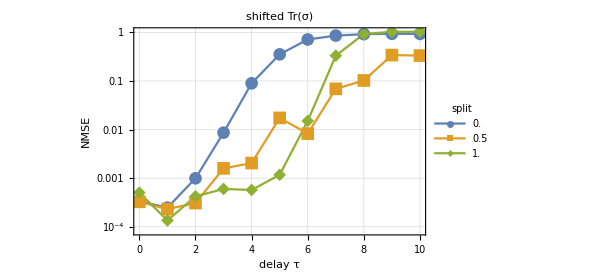

```mathematica
With[
{
listmeanresults=listresultsTr//Mean
},
plotresultsTr=ListLogPlot[
listmeanresultsᵀ,
Joined->True,
Frame->True,
ImageSize->450,LabelStyle->15,
GridLines->Automatic,
(*PlotLegends->listbigR,*)
PlotLabel->"shifted Tr(σ)",
PlotLegends->PointLegend[listτsplit,LegendLabel->"split"],
FrameLabel->{"delay τ","NMSE"},
PlotRange->All,
PlotMarkers->{Automatic,13},
DataRange->MinMax[listτ]
]
]
```

### Show plots

```mathematica
plotresultsTr
```

-Graphics-

## Determinant

```mathematica
seed=192467;
```

### Generate the task

#### Parameters for the task

```mathematica
{prep,train,test}={500,3000,1000};
listτ=Range[0,10];
```

#### The task proper

```mathematica
{getrandominput,gettarget,figureofmerit}=makeElementTask[];
getfinaltarget=makeDetTask[][[2]];
```

### Parameters for the RC

#### Parameters for the Q reservoir

```mathematica
n=9;
bigR=0.4;
p=7./9;
```

```mathematica
listτsplit={0.,0.5,1.}
```

{0.,0.5,1.}

#### Parameters for the ESN RC

```mathematica
nESN=(n^2-n)/2+n;
ρ0=0.1; 
ι0=0.01; 
pESN=1.;
spatESN=1;
myafun={Tanh(*Tanh*),Ramp(*ReLu*),Function[x,Ramp[x]-0.01Ramp[-x]](*leaky ReLu*),Function[x,x](*identity (linear ESN)*),Function[x,Log[1.+Exp[x]]](*softmax*)}[[-1]];
```

### Computations

```mathematica
SeedRandom[seed];
```

```mathematica
done=0;SetSharedVariable[done]
```

```mathematica
Monitor[listresultsDet=ParallelTable[
(*create random input*)
listinput=getrandominput[prep+train+test];
(*create a QRC instance*)
{update,getinit,preprocess,readout}=makerandomJorgeQRCforQinput[n,bigR,p,bigM];
(*get the observables, sampling noise taken care of by readout*)
listobservables=getobservables[update,getinit[],preprocess,listinput,readout];
(*all targets for this delay*)
listtarget11=gettarget[listinput,1,1,Ceiling[(1-τsplit)delay]]//Function[listtarget,listtarget-Mean[listtarget]];
listtarget12=gettarget[listinput,1,2,Ceiling[(1-τsplit)delay]]//Function[listtarget,listtarget-Mean[listtarget]];
listtarget22=gettarget[listinput,2,2,Ceiling[(1-τsplit)delay]]//Function[listtarget,listtarget-Mean[listtarget]];
listtarget=getfinaltarget[listinput,delay];
shift=Mean[listtarget];
listtarget-=shift;
(*call trainertester*)
{NMSE11,getoutput11}=trainertester[listobservables,listtarget11,prep,train,test];
{NMSE12,getoutput12}=trainertester[listobservables,listtarget12,prep,train,test];
{NMSE22,getoutput22}=trainertester[listobservables,listtarget22,prep,train,test];
(*create an ESN instance*)
{updateESN,getrandominitESN,preprocessESN,readoutESN}=makerandomESNcoerced[nESN,ρ0,ι0,myafun,pESN,spatESN,4];
(*collect all QRC outputs together for the ESN*)
listinputESN={getoutput11[listobservables],getoutput12[listobservables],getoutput12[listobservables],getoutput22[listobservables]}ᵀ;
(*get the ESN observables*)
listobservablesESN=getobservables[updateESN,getrandominitESN[],preprocessESN,listinputESN,readoutESN];
(**)
{NMSEofSandwich,getoutputSandwich}=trainertester[Join[listobservablesESN,listobservables,2],listtarget,prep,train,test];
(*increment done*)
done+=1;
(*the final NMSEs*)
NMSEofSandwich,{reps},{delay,listτ},{τsplit,listτsplit}
],ProgressIndicator[done,{0,reps Length[listτ]Length[listτsplit]}]];//AbsoluteTiming//First
```

46.7095

### Make some plots

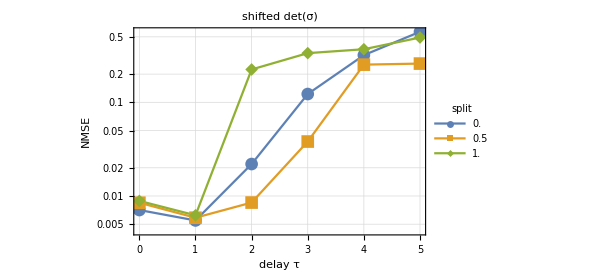

```mathematica
With[
{
listmeanresults=listresultsDet//Mean
},
plotresultsDet=ListLogPlot[
(listmeanresultsᵀ)[[All,;;6]],
Joined->True,
Frame->True,
ImageSize->450,LabelStyle->15,
GridLines->Automatic,
PlotLegends->PointLegend[listτsplit,LegendLabel->"split"],
PlotLabel->"shifted det(σ)",
FrameLabel->{"delay τ",Style["NMSE",White]},
PlotRange->All,
PlotMarkers->{Automatic,13},
DataRange->MinMax[listτ[[;;6]]]
]
]
```

### Show plots

```mathematica
plotresultsDet
```

-Graphics-

## Combination plot

### Make the plot

```mathematica
With[
{
upto=9,
listmedianresults=Join[(listresultsTr//Mean)ᵀ,(listresultsDet//Mean)ᵀ]
},
With[
{
listmedianresultsTrcalled=MapAt[Callout[#,Style["shifted Tr(σ)",13],Bottom,"CalloutStyle"->Darker@Gray]&,listmedianresults,{3,4}]
},
With[
{
listmedianresultsbothcalled=MapAt[Callout[#,Style["shifted Det(σ)",13],Top,"CalloutStyle"->Darker@Gray]&,listmedianresultsTrcalled,{6,3}]
},
plotτsplitresults=ListLogPlot[
listmedianresultsbothcalled[[All,;;upto]],
Joined->True,
Frame->True,
ImageSize->450,LabelStyle->15,
GridLines->Automatic,
PlotLegends->Placed[PointLegend[{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885]},{Style["τ'=τ",15,FontFamily->"Helvetica"],Style["τ'=⌈τ/2⌉",15,FontFamily->"Helvetica"],Style["τ'=0",15,FontFamily->"Helvetica"]},LegendMarkers->{{"●","■","◆"},ConstantArray[13,3]}ᵀ,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->Thin,Background->White]&)],Scaled[{0.85,0.27}]],
FrameLabel->{"delay τ","NMSE"},
PlotRange->All,
PlotStyle->{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],Directive[Dashed,RGBColor[0.368417, 0.506779, 0.709798]],Directive[Dashed,RGBColor[0.880722, 0.611041, 0.142051]],Directive[Dashed,RGBColor[0.560181, 0.691569, 0.194885]]},
PlotMarkers->{{"●","■","◆","●","■","◆"},ConstantArray[15,6]}ᵀ,
DataRange->MinMax[listτ[[;;upto]]]
]
]
]
]
```

-Graphics-

### Show the plot

```mathematica
plotτsplitresults
```

-Graphics-